```mathematica
<<HighPT`
```

-Graphics-

Authors: Lukas Allwicher, Darius A. Faroughy, Florentin Jaffredo, Olcyr Sumensari, and Felix Wilsch

References: arXiv:2207.10756http://arxiv.org/abs/2207.10756Nonehttp://arxiv.org/abs/2207.10756HyperlinkHyperlinkActive, arXiv:2207.10714http://arxiv.org/abs/2207.10714Nonehttp://arxiv.org/abs/2207.10714HyperlinkHyperlinkActive

Website: https://highpt.github.iohttps://highpt.github.ioNonehttps://highpt.github.ioHyperlinkHyperlinkActive

HighPT is free software released under the terms of the MIT License.

Version: 1.0.2

____________________________________

Initialized SMEFT mode:

Maximum operator dimension: 6

EFT series truncation at: Λ_NP^-4

EFT cutoff scale Λ_NP: 1. TeV

## C_eu

```mathematica
EUchi2binned=ChiSquareLHC["di-electron-CMS",Coefficients->{WC["eu",{1,1,1,2}]}]
```

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{1.31229×10^-7 (-220.-908.457 WC[eu,{1,1,1,2}]^2)^2,4.79709×10^-7 (-508.-998.341 WC[eu,{1,1,1,2}]^2)^2,8.32932×10^-7 (-186.-1025.33 WC[eu,{1,1,1,2}]^2)^2,1.42801×10^-6 (-102.8-1038.9 WC[eu,{1,1,1,2}]^2)^2,2.91439×10^-6 (-95.8-1032.48 WC[eu,{1,1,1,2}]^2)^2,3.77702×10^-6 (25.4-1022.85 WC[eu,{1,1,1,2}]^2)^2,6.59321×10^-6 (-80.2-1045.77 WC[eu,{1,1,1,2}]^2)^2,0.0000119208 (10.-1013.99 WC[eu,{1,1,1,2}]^2)^2,0.0000136098 (-92.6-1016. WC[eu,{1,1,1,2}]^2)^2,0.000026548 (-127.2-992.033 WC[eu,{1,1,1,2}]^2)^2,0.0000289728 (-39.8-995.087 WC[eu,{1,1,1,2}]^2)^2,0.0000610597 (15.2-977.541 WC[eu,{1,1,1,2}]^2)^2,0.0000781328 (24.-964.178 WC[eu,{1,1,1,2}]^2)^2,0.000132442 (-85.9-948.138 WC[eu,{1,1,1,2}]^2)^2,0.000175753 (-70.3-923.534 WC[eu,{1,1,1,2}]^2)^2,0.000158207 (-34.16-907.861 WC[eu,{1,1,1,2}]^2)^2,0.000303825 (-8.72-893.364 WC[eu,{1,1,1,2}]^2)^2,0.000400252 (-29.48-861.507 WC[eu,{1,1,1,2}]^2)^2,0.000474043 (9.46-859.749 WC[eu,{1,1,1,2}]^2)^2,0.000597818 (20.2-839.307 WC[eu,{1,1,1,2}]^2)^2,0.00028771 (13.24-1196.25 WC[eu,{1,1,1,2}]^2)^2,0.00067054 (9.24-1200.09 WC[eu,{1,1,1,2}]^2)^2,0.000826956 (1.31-1146.86 WC[eu,{1,1,1,2}]^2)^2,0.00103064 (20.23-1087.61 WC[eu,{1,1,1,2}]^2)^2,0.00138021 (43.85-1063.4 WC[eu,{1,1,1,2}]^2)^2,0.00172993 (44.09-1015.57 WC[eu,{1,1,1,2}]^2)^2,0.00225394 (-39.474-970.624 WC[eu,{1,1,1,2}]^2)^2,0.00205416 (20.313-943.463 WC[eu,{1,1,1,2}]^2)^2,0.00439089 (-3.942-915.982 WC[eu,{1,1,1,2}]^2)^2,0.00550609 (-10.403-893.9 WC[eu,{1,1,1,2}]^2)^2,0.00277449 (-3.095-1390.54 WC[eu,{1,1,1,2}]^2)^2,0.00447406 (19.095-1323.94 WC[eu,{1,1,1,2}]^2)^2,0.00784357 (-19.805-1213.84 WC[eu,{1,1,1,2}]^2)^2,0.00876178 (-1.795-1147.82 WC[eu,{1,1,1,2}]^2)^2,0.0101038 (13.785-1112.2 WC[eu,{1,1,1,2}]^2)^2,0.0159493 (-3.115-980.79 WC[eu,{1,1,1,2}]^2)^2,0.0193558 (-0.3115-941.599 WC[eu,{1,1,1,2}]^2)^2,0.0173414 (3.643-1051.2 WC[eu,{1,1,1,2}]^2)^2,0.0257042 (1.4852-990.881 WC[eu,{1,1,1,2}]^2)^2,0.0390994 (-2.7774-902.525 WC[eu,{1,1,1,2}]^2)^2,0.0361578 (5.8864-854.172 WC[eu,{1,1,1,2}]^2)^2,0.058422 (-0.0264-771.851 WC[eu,{1,1,1,2}]^2)^2,0.0392055 (-0.3364-1481.13 WC[eu,{1,1,1,2}]^2)^2,0.0549663 (1.64935-1346.73 WC[eu,{1,1,1,2}]^2)^2,0.0603729 (6.03191-1197.76 WC[eu,{1,1,1,2}]^2)^2,0.0811921 (3.32544-1483.94 WC[eu,{1,1,1,2}]^2)^2,0.0708141 (5.30038-3987.61 WC[eu,{1,1,1,2}]^2)^2}

```mathematica
Length[EUchi2binned]
```

47

```mathematica
WC/:Conjugate[WC[a___]]:=WC[a]
```

```mathematica
EUchi2=Total[EUchi2binned]
```

0.0708141 (5.30038-3987.61 WC[eu,{1,1,1,2}]^2)^2+0.0811921 (3.32544-1483.94 WC[eu,{1,1,1,2}]^2)^2+0.0392055 (-0.3364-1481.13 WC[eu,{1,1,1,2}]^2)^2+0.00277449 (-3.095-1390.54 WC[eu,{1,1,1,2}]^2)^2+0.0549663 (1.64935-1346.73 WC[eu,{1,1,1,2}]^2)^2+0.00447406 (19.095-1323.94 WC[eu,{1,1,1,2}]^2)^2+0.00784357 (-19.805-1213.84 WC[eu,{1,1,1,2}]^2)^2+0.00067054 (9.24-1200.09 WC[eu,{1,1,1,2}]^2)^2+0.0603729 (6.03191-1197.76 WC[eu,{1,1,1,2}]^2)^2+0.00028771 (13.24-1196.25 WC[eu,{1,1,1,2}]^2)^2+0.00876178 (-1.795-1147.82 WC[eu,{1,1,1,2}]^2)^2+0.000826956 (1.31-1146.86 WC[eu,{1,1,1,2}]^2)^2+0.0101038 (13.785-1112.2 WC[eu,{1,1,1,2}]^2)^2+0.00103064 (20.23-1087.61 WC[eu,{1,1,1,2}]^2)^2+0.00138021 (43.85-1063.4 WC[eu,{1,1,1,2}]^2)^2+0.0173414 (3.643-1051.2 WC[eu,{1,1,1,2}]^2)^2+6.59321×10^-6 (-80.2-1045.77 WC[eu,{1,1,1,2}]^2)^2+1.42801×10^-6 (-102.8-1038.9 WC[eu,{1,1,1,2}]^2)^2+2.91439×10^-6 (-95.8-1032.48 WC[eu,{1,1,1,2}]^2)^2+8.32932×10^-7 (-186.-1025.33 WC[eu,{1,1,1,2}]^2)^2+3.77702×10^-6 (25.4-1022.85 WC[eu,{1,1,1,2}]^2)^2+0.0000136098 (-92.6-1016. WC[eu,{1,1,1,2}]^2)^2+0.00172993 (44.09-1015.57 WC[eu,{1,1,1,2}]^2)^2+0.0000119208 (10.-1013.99 WC[eu,{1,1,1,2}]^2)^2+4.79709×10^-7 (-508.-998.341 WC[eu,{1,1,1,2}]^2)^2+0.0000289728 (-39.8-995.087 WC[eu,{1,1,1,2}]^2)^2+0.000026548 (-127.2-992.033 WC[eu,{1,1,1,2}]^2)^2+0.0257042 (1.4852-990.881 WC[eu,{1,1,1,2}]^2)^2+0.0159493 (-3.115-980.79 WC[eu,{1,1,1,2}]^2)^2+0.0000610597 (15.2-977.541 WC[eu,{1,1,1,2}]^2)^2+0.00225394 (-39.474-970.624 WC[eu,{1,1,1,2}]^2)^2+0.0000781328 (24.-964.178 WC[eu,{1,1,1,2}]^2)^2+0.000132442 (-85.9-948.138 WC[eu,{1,1,1,2}]^2)^2+0.00205416 (20.313-943.463 WC[eu,{1,1,1,2}]^2)^2+0.0193558 (-0.3115-941.599 WC[eu,{1,1,1,2}]^2)^2+0.000175753 (-70.3-923.534 WC[eu,{1,1,1,2}]^2)^2+0.00439089 (-3.942-915.982 WC[eu,{1,1,1,2}]^2)^2+1.31229×10^-7 (-220.-908.457 WC[eu,{1,1,1,2}]^2)^2+0.000158207 (-34.16-907.861 WC[eu,{1,1,1,2}]^2)^2+0.0390994 (-2.7774-902.525 WC[eu,{1,1,1,2}]^2)^2+0.00550609 (-10.403-893.9 WC[eu,{1,1,1,2}]^2)^2+0.000303825 (-8.72-893.364 WC[eu,{1,1,1,2}]^2)^2+0.000400252 (-29.48-861.507 WC[eu,{1,1,1,2}]^2)^2+0.000474043 (9.46-859.749 WC[eu,{1,1,1,2}]^2)^2+0.0361578 (5.8864-854.172 WC[eu,{1,1,1,2}]^2)^2+0.000597818 (20.2-839.307 WC[eu,{1,1,1,2}]^2)^2+0.058422 (-0.0264-771.851 WC[eu,{1,1,1,2}]^2)^2

```mathematica
{min,bestfit}=NMinimize[EUchi2,{WC["eu",{1,1,1,2}]}]
```

{25.2055,{WC[eu,{1,1,1,2}]→0.0382039}}

```mathematica
Solve[EUchi2==min+3.841,WC["eu",{1,1,1,2}]]
```

{{WC[eu,{1,1,1,2}]→-0.0539771},{WC[eu,{1,1,1,2}]→-0.00235559},{WC[eu,{1,1,1,2}]→0.00235559},{WC[eu,{1,1,1,2}]→0.0539771}}

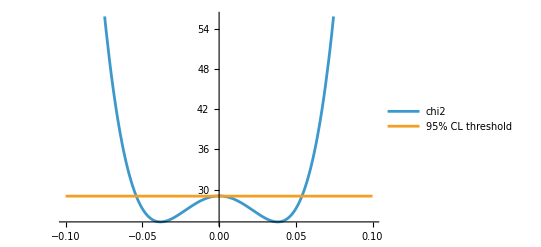

```mathematica
Plot[{EUchi2,min+3.841},{WC["eu",{1,1,1,2}],-0.1,0.1},PlotLegends->{"chi2","95% CL threshold"}]
```

## C_lq1

```mathematica
LQ1chi2binned=ChiSquareLHC["di-electron-CMS",Coefficients->{WC["lq1",{1,1,1,2}]}]
```

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{1.31229×10^-7 ((-220.+0. ⅈ)+(1971.22+0. ⅈ) WC[lq1,{1,1,1,2}]-1977.33 WC[lq1,{1,1,1,2}]^2)^2,4.79709×10^-7 ((-508.+0. ⅈ)+(1820.42+0. ⅈ) WC[lq1,{1,1,1,2}]-2137.67 WC[lq1,{1,1,1,2}]^2)^2,8.32932×10^-7 ((-186.+0. ⅈ)+(1616.05+0. ⅈ) WC[lq1,{1,1,1,2}]-2160.67 WC[lq1,{1,1,1,2}]^2)^2,1.42801×10^-6 ((-102.8+0. ⅈ)+(1405.93+0. ⅈ) WC[lq1,{1,1,1,2}]-2218.92 WC[lq1,{1,1,1,2}]^2)^2,2.91439×10^-6 ((-95.8+0. ⅈ)+(1241.76+0. ⅈ) WC[lq1,{1,1,1,2}]-2186.9 WC[lq1,{1,1,1,2}]^2)^2,3.77702×10^-6 ((25.4+0. ⅈ)+(1129.6+0. ⅈ) WC[lq1,{1,1,1,2}]-2155.34 WC[lq1,{1,1,1,2}]^2)^2,6.59321×10^-6 ((-80.2+0. ⅈ)+(1009.1+0. ⅈ) WC[lq1,{1,1,1,2}]-2125.6 WC[lq1,{1,1,1,2}]^2)^2,0.0000119208 ((10.+0. ⅈ)+(924.341+0. ⅈ) WC[lq1,{1,1,1,2}]-2127.37 WC[lq1,{1,1,1,2}]^2)^2,0.0000136098 ((-92.6+0. ⅈ)+(844.348+0. ⅈ) WC[lq1,{1,1,1,2}]-2116.92 WC[lq1,{1,1,1,2}]^2)^2,0.000026548 ((-127.2+0. ⅈ)+(770.357+0. ⅈ) WC[lq1,{1,1,1,2}]-2071.4 WC[lq1,{1,1,1,2}]^2)^2,0.0000289728 ((-39.8+0. ⅈ)+(679.736+0. ⅈ) WC[lq1,{1,1,1,2}]-2026.74 WC[lq1,{1,1,1,2}]^2)^2,0.0000610597 ((15.2+0. ⅈ)+(615.3+0. ⅈ) WC[lq1,{1,1,1,2}]-2007.09 WC[lq1,{1,1,1,2}]^2)^2,0.0000781328 ((24.+0. ⅈ)+(574.169+0. ⅈ) WC[lq1,{1,1,1,2}]-1976.02 WC[lq1,{1,1,1,2}]^2)^2,0.000132442 ((-85.9+0. ⅈ)+(523.503+0. ⅈ) WC[lq1,{1,1,1,2}]-1922.06 WC[lq1,{1,1,1,2}]^2)^2,0.000175753 ((-70.3+0. ⅈ)+(472.712+0. ⅈ) WC[lq1,{1,1,1,2}]-1876.46 WC[lq1,{1,1,1,2}]^2)^2,0.000158207 ((-34.16+0. ⅈ)+(437.127+0. ⅈ) WC[lq1,{1,1,1,2}]-1831.37 WC[lq1,{1,1,1,2}]^2)^2,0.000303825 ((-8.72+0. ⅈ)+(398.252+0. ⅈ) WC[lq1,{1,1,1,2}]-1801.52 WC[lq1,{1,1,1,2}]^2)^2,0.000400252 ((-29.48+0. ⅈ)+(367.848+0. ⅈ) WC[lq1,{1,1,1,2}]-1742.87 WC[lq1,{1,1,1,2}]^2)^2,0.000474043 ((9.46+0. ⅈ)+(345.505+0. ⅈ) WC[lq1,{1,1,1,2}]-1714.37 WC[lq1,{1,1,1,2}]^2)^2,0.000597818 ((20.2+0. ⅈ)+(317.224+0. ⅈ) WC[lq1,{1,1,1,2}]-1671.07 WC[lq1,{1,1,1,2}]^2)^2,0.00028771 ((13.24+0. ⅈ)+(426.106+0. ⅈ) WC[lq1,{1,1,1,2}]-2399.69 WC[lq1,{1,1,1,2}]^2)^2,0.00067054 ((9.24+0. ⅈ)+(382.288+0. ⅈ) WC[lq1,{1,1,1,2}]-2375.07 WC[lq1,{1,1,1,2}]^2)^2,0.000826956 ((1.31+0. ⅈ)+(350.835+0. ⅈ) WC[lq1,{1,1,1,2}]-2265.21 WC[lq1,{1,1,1,2}]^2)^2,0.00103064 ((20.23+0. ⅈ)+(313.043+0. ⅈ) WC[lq1,{1,1,1,2}]-2143.18 WC[lq1,{1,1,1,2}]^2)^2,0.00138021 ((43.85+0. ⅈ)+(281.716+0. ⅈ) WC[lq1,{1,1,1,2}]-2098.59 WC[lq1,{1,1,1,2}]^2)^2,0.00172993 ((44.09+0. ⅈ)+(255.373+0. ⅈ) WC[lq1,{1,1,1,2}]-2014.57 WC[lq1,{1,1,1,2}]^2)^2,0.00225394 ((-39.474+0. ⅈ)+(226.822+0. ⅈ) WC[lq1,{1,1,1,2}]-1923.15 WC[lq1,{1,1,1,2}]^2)^2,0.00205416 ((20.313+0. ⅈ)+(204.724+0. ⅈ) WC[lq1,{1,1,1,2}]-1850.7 WC[lq1,{1,1,1,2}]^2)^2,0.00439089 ((-3.942+0. ⅈ)+(190.967+0. ⅈ) WC[lq1,{1,1,1,2}]-1786.64 WC[lq1,{1,1,1,2}]^2)^2,0.00550609 ((-10.403+0. ⅈ)+(173.949+0. ⅈ) WC[lq1,{1,1,1,2}]-1720.23 WC[lq1,{1,1,1,2}]^2)^2,0.00277449 ((-3.095+0. ⅈ)+(253.185+0. ⅈ) WC[lq1,{1,1,1,2}]-2709.2 WC[lq1,{1,1,1,2}]^2)^2,0.00447406 ((19.095+0. ⅈ)+(218.615+0. ⅈ) WC[lq1,{1,1,1,2}]-2548.36 WC[lq1,{1,1,1,2}]^2)^2,0.00784357 ((-19.805+0. ⅈ)+(187.287+0. ⅈ) WC[lq1,{1,1,1,2}]-2372.27 WC[lq1,{1,1,1,2}]^2)^2,0.00876178 ((-1.795+0. ⅈ)+(164.826+0. ⅈ) WC[lq1,{1,1,1,2}]-2228.48 WC[lq1,{1,1,1,2}]^2)^2,0.0101038 ((13.785+0. ⅈ)+(141.641+0. ⅈ) WC[lq1,{1,1,1,2}]-2105.64 WC[lq1,{1,1,1,2}]^2)^2,0.0159493 ((-3.115+0. ⅈ)+(123.104+0. ⅈ) WC[lq1,{1,1,1,2}]-1886.82 WC[lq1,{1,1,1,2}]^2)^2,0.0193558 ((-0.3115+0. ⅈ)+(108.872+0. ⅈ) WC[lq1,{1,1,1,2}]-1796.97 WC[lq1,{1,1,1,2}]^2)^2,0.0173414 ((3.643+0. ⅈ)+(113.295+0. ⅈ) WC[lq1,{1,1,1,2}]-2009.23 WC[lq1,{1,1,1,2}]^2)^2,0.0257042 ((1.4852+0. ⅈ)+(96.7512+0. ⅈ) WC[lq1,{1,1,1,2}]-1881.47 WC[lq1,{1,1,1,2}]^2)^2,0.0390994 ((-2.7774+0. ⅈ)+(85.1546+0. ⅈ) WC[lq1,{1,1,1,2}]-1701.03 WC[lq1,{1,1,1,2}]^2)^2,0.0361578 ((5.8864+0. ⅈ)+(71.8978+0. ⅈ) WC[lq1,{1,1,1,2}]-1596.25 WC[lq1,{1,1,1,2}]^2)^2,0.058422 ((-0.0264+0. ⅈ)+(62.3205+0. ⅈ) WC[lq1,{1,1,1,2}]-1456.75 WC[lq1,{1,1,1,2}]^2)^2,0.0392055 ((-0.3364+0. ⅈ)+(109.313+0. ⅈ) WC[lq1,{1,1,1,2}]-2781.26 WC[lq1,{1,1,1,2}]^2)^2,0.0549663 ((1.64935+0. ⅈ)+(85.9601+0. ⅈ) WC[lq1,{1,1,1,2}]-2513.91 WC[lq1,{1,1,1,2}]^2)^2,0.0603729 ((6.03191+0. ⅈ)+(67.4093+0. ⅈ) WC[lq1,{1,1,1,2}]-2229.99 WC[lq1,{1,1,1,2}]^2)^2,0.0811921 ((3.32544+0. ⅈ)+(71.6295+0. ⅈ) WC[lq1,{1,1,1,2}]-2771.23 WC[lq1,{1,1,1,2}]^2)^2,0.0708141 ((5.30038+0. ⅈ)+(118.979+0. ⅈ) WC[lq1,{1,1,1,2}]-7201.42 WC[lq1,{1,1,1,2}]^2)^2}

```mathematica
LQ1chi2binned // Length
```

47

```mathematica
WC/:Conjugate[WC[a___]]:=WC[a]
```

```mathematica
LQ1chi2=Total[LQ1chi2binned]
```

0.0708141 ((5.30038+0. ⅈ)+(118.979+0. ⅈ) WC[lq1,{1,1,1,2}]-7201.42 WC[lq1,{1,1,1,2}]^2)^2+0.0392055 ((-0.3364+0. ⅈ)+(109.313+0. ⅈ) WC[lq1,{1,1,1,2}]-2781.26 WC[lq1,{1,1,1,2}]^2)^2+0.0811921 ((3.32544+0. ⅈ)+(71.6295+0. ⅈ) WC[lq1,{1,1,1,2}]-2771.23 WC[lq1,{1,1,1,2}]^2)^2+0.00277449 ((-3.095+0. ⅈ)+(253.185+0. ⅈ) WC[lq1,{1,1,1,2}]-2709.2 WC[lq1,{1,1,1,2}]^2)^2+0.00447406 ((19.095+0. ⅈ)+(218.615+0. ⅈ) WC[lq1,{1,1,1,2}]-2548.36 WC[lq1,{1,1,1,2}]^2)^2+0.0549663 ((1.64935+0. ⅈ)+(85.9601+0. ⅈ) WC[lq1,{1,1,1,2}]-2513.91 WC[lq1,{1,1,1,2}]^2)^2+0.00028771 ((13.24+0. ⅈ)+(426.106+0. ⅈ) WC[lq1,{1,1,1,2}]-2399.69 WC[lq1,{1,1,1,2}]^2)^2+0.00067054 ((9.24+0. ⅈ)+(382.288+0. ⅈ) WC[lq1,{1,1,1,2}]-2375.07 WC[lq1,{1,1,1,2}]^2)^2+0.00784357 ((-19.805+0. ⅈ)+(187.287+0. ⅈ) WC[lq1,{1,1,1,2}]-2372.27 WC[lq1,{1,1,1,2}]^2)^2+0.000826956 ((1.31+0. ⅈ)+(350.835+0. ⅈ) WC[lq1,{1,1,1,2}]-2265.21 WC[lq1,{1,1,1,2}]^2)^2+0.0603729 ((6.03191+0. ⅈ)+(67.4093+0. ⅈ) WC[lq1,{1,1,1,2}]-2229.99 WC[lq1,{1,1,1,2}]^2)^2+0.00876178 ((-1.795+0. ⅈ)+(164.826+0. ⅈ) WC[lq1,{1,1,1,2}]-2228.48 WC[lq1,{1,1,1,2}]^2)^2+1.42801×10^-6 ((-102.8+0. ⅈ)+(1405.93+0. ⅈ) WC[lq1,{1,1,1,2}]-2218.92 WC[lq1,{1,1,1,2}]^2)^2+2.91439×10^-6 ((-95.8+0. ⅈ)+(1241.76+0. ⅈ) WC[lq1,{1,1,1,2}]-2186.9 WC[lq1,{1,1,1,2}]^2)^2+8.32932×10^-7 ((-186.+0. ⅈ)+(1616.05+0. ⅈ) WC[lq1,{1,1,1,2}]-2160.67 WC[lq1,{1,1,1,2}]^2)^2+3.77702×10^-6 ((25.4+0. ⅈ)+(1129.6+0. ⅈ) WC[lq1,{1,1,1,2}]-2155.34 WC[lq1,{1,1,1,2}]^2)^2+0.00103064 ((20.23+0. ⅈ)+(313.043+0. ⅈ) WC[lq1,{1,1,1,2}]-2143.18 WC[lq1,{1,1,1,2}]^2)^2+4.79709×10^-7 ((-508.+0. ⅈ)+(1820.42+0. ⅈ) WC[lq1,{1,1,1,2}]-2137.67 WC[lq1,{1,1,1,2}]^2)^2+0.0000119208 ((10.+0. ⅈ)+(924.341+0. ⅈ) WC[lq1,{1,1,1,2}]-2127.37 WC[lq1,{1,1,1,2}]^2)^2+6.59321×10^-6 ((-80.2+0. ⅈ)+(1009.1+0. ⅈ) WC[lq1,{1,1,1,2}]-2125.6 WC[lq1,{1,1,1,2}]^2)^2+0.0000136098 ((-92.6+0. ⅈ)+(844.348+0. ⅈ) WC[lq1,{1,1,1,2}]-2116.92 WC[lq1,{1,1,1,2}]^2)^2+0.0101038 ((13.785+0. ⅈ)+(141.641+0. ⅈ) WC[lq1,{1,1,1,2}]-2105.64 WC[lq1,{1,1,1,2}]^2)^2+0.00138021 ((43.85+0. ⅈ)+(281.716+0. ⅈ) WC[lq1,{1,1,1,2}]-2098.59 WC[lq1,{1,1,1,2}]^2)^2+0.000026548 ((-127.2+0. ⅈ)+(770.357+0. ⅈ) WC[lq1,{1,1,1,2}]-2071.4 WC[lq1,{1,1,1,2}]^2)^2+0.0000289728 ((-39.8+0. ⅈ)+(679.736+0. ⅈ) WC[lq1,{1,1,1,2}]-2026.74 WC[lq1,{1,1,1,2}]^2)^2+0.00172993 ((44.09+0. ⅈ)+(255.373+0. ⅈ) WC[lq1,{1,1,1,2}]-2014.57 WC[lq1,{1,1,1,2}]^2)^2+0.0173414 ((3.643+0. ⅈ)+(113.295+0. ⅈ) WC[lq1,{1,1,1,2}]-2009.23 WC[lq1,{1,1,1,2}]^2)^2+0.0000610597 ((15.2+0. ⅈ)+(615.3+0. ⅈ) WC[lq1,{1,1,1,2}]-2007.09 WC[lq1,{1,1,1,2}]^2)^2+1.31229×10^-7 ((-220.+0. ⅈ)+(1971.22+0. ⅈ) WC[lq1,{1,1,1,2}]-1977.33 WC[lq1,{1,1,1,2}]^2)^2+0.0000781328 ((24.+0. ⅈ)+(574.169+0. ⅈ) WC[lq1,{1,1,1,2}]-1976.02 WC[lq1,{1,1,1,2}]^2)^2+0.00225394 ((-39.474+0. ⅈ)+(226.822+0. ⅈ) WC[lq1,{1,1,1,2}]-1923.15 WC[lq1,{1,1,1,2}]^2)^2+0.000132442 ((-85.9+0. ⅈ)+(523.503+0. ⅈ) WC[lq1,{1,1,1,2}]-1922.06 WC[lq1,{1,1,1,2}]^2)^2+0.0159493 ((-3.115+0. ⅈ)+(123.104+0. ⅈ) WC[lq1,{1,1,1,2}]-1886.82 WC[lq1,{1,1,1,2}]^2)^2+0.0257042 ((1.4852+0. ⅈ)+(96.7512+0. ⅈ) WC[lq1,{1,1,1,2}]-1881.47 WC[lq1,{1,1,1,2}]^2)^2+0.000175753 ((-70.3+0. ⅈ)+(472.712+0. ⅈ) WC[lq1,{1,1,1,2}]-1876.46 WC[lq1,{1,1,1,2}]^2)^2+0.00205416 ((20.313+0. ⅈ)+(204.724+0. ⅈ) WC[lq1,{1,1,1,2}]-1850.7 WC[lq1,{1,1,1,2}]^2)^2+0.000158207 ((-34.16+0. ⅈ)+(437.127+0. ⅈ) WC[lq1,{1,1,1,2}]-1831.37 WC[lq1,{1,1,1,2}]^2)^2+0.000303825 ((-8.72+0. ⅈ)+(398.252+0. ⅈ) WC[lq1,{1,1,1,2}]-1801.52 WC[lq1,{1,1,1,2}]^2)^2+0.0193558 ((-0.3115+0. ⅈ)+(108.872+0. ⅈ) WC[lq1,{1,1,1,2}]-1796.97 WC[lq1,{1,1,1,2}]^2)^2+0.00439089 ((-3.942+0. ⅈ)+(190.967+0. ⅈ) WC[lq1,{1,1,1,2}]-1786.64 WC[lq1,{1,1,1,2}]^2)^2+0.000400252 ((-29.48+0. ⅈ)+(367.848+0. ⅈ) WC[lq1,{1,1,1,2}]-1742.87 WC[lq1,{1,1,1,2}]^2)^2+0.00550609 ((-10.403+0. ⅈ)+(173.949+0. ⅈ) WC[lq1,{1,1,1,2}]-1720.23 WC[lq1,{1,1,1,2}]^2)^2+0.000474043 ((9.46+0. ⅈ)+(345.505+0. ⅈ) WC[lq1,{1,1,1,2}]-1714.37 WC[lq1,{1,1,1,2}]^2)^2+0.0390994 ((-2.7774+0. ⅈ)+(85.1546+0. ⅈ) WC[lq1,{1,1,1,2}]-1701.03 WC[lq1,{1,1,1,2}]^2)^2+0.000597818 ((20.2+0. ⅈ)+(317.224+0. ⅈ) WC[lq1,{1,1,1,2}]-1671.07 WC[lq1,{1,1,1,2}]^2)^2+0.0361578 ((5.8864+0. ⅈ)+(71.8978+0. ⅈ) WC[lq1,{1,1,1,2}]-1596.25 WC[lq1,{1,1,1,2}]^2)^2+0.058422 ((-0.0264+0. ⅈ)+(62.3205+0. ⅈ) WC[lq1,{1,1,1,2}]-1456.75 WC[lq1,{1,1,1,2}]^2)^2

```mathematica
{min,bestfit}=NMinimize[LQ1chi2,{WC["lq1",{1,1,1,2}]}]
```

{26.4608+0. ⅈ,{WC[lq1,{1,1,1,2}]→-0.015145+0. ⅈ}}

```mathematica
Solve[LQ1chi2==min+3.841,WC["lq1",{1,1,1,2}]]
```

{{WC[lq1,{1,1,1,2}]→-0.0265658},{WC[lq1,{1,1,1,2}]→0.00619463},{WC[lq1,{1,1,1,2}]→0.0241792},{WC[lq1,{1,1,1,2}]→0.0503483}}

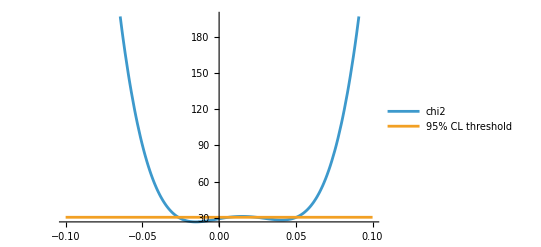

```mathematica
Plot[{LQ1chi2,min+3.841},{WC["lq1",{1,1,1,2}],-0.1,0.1},PlotLegends->{"chi2","95% CL threshold"}]
```

## C_lq3

```mathematica
LQ3chi2binned=ChiSquareLHC["di-electron-CMS",Coefficients->{WC["lq3",{1,1,1,2}]}]
```

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{1.31229×10^-7 ((-220.+0. ⅈ)-(1971.22+0. ⅈ) WC[lq3,{1,1,1,2}]-1977.33 WC[lq3,{1,1,1,2}]^2)^2,4.79709×10^-7 ((-508.+0. ⅈ)-(1820.42+0. ⅈ) WC[lq3,{1,1,1,2}]-2137.67 WC[lq3,{1,1,1,2}]^2)^2,8.32932×10^-7 ((-186.+0. ⅈ)-(1616.05+0. ⅈ) WC[lq3,{1,1,1,2}]-2160.67 WC[lq3,{1,1,1,2}]^2)^2,1.42801×10^-6 ((-102.8+0. ⅈ)-(1405.93+0. ⅈ) WC[lq3,{1,1,1,2}]-2218.92 WC[lq3,{1,1,1,2}]^2)^2,2.91439×10^-6 ((-95.8+0. ⅈ)-(1241.76+0. ⅈ) WC[lq3,{1,1,1,2}]-2186.9 WC[lq3,{1,1,1,2}]^2)^2,3.77702×10^-6 ((25.4+0. ⅈ)-(1129.6+0. ⅈ) WC[lq3,{1,1,1,2}]-2155.34 WC[lq3,{1,1,1,2}]^2)^2,6.59321×10^-6 ((-80.2+0. ⅈ)-(1009.1+0. ⅈ) WC[lq3,{1,1,1,2}]-2125.6 WC[lq3,{1,1,1,2}]^2)^2,0.0000119208 ((10.+0. ⅈ)-(924.341+0. ⅈ) WC[lq3,{1,1,1,2}]-2127.37 WC[lq3,{1,1,1,2}]^2)^2,0.0000136098 ((-92.6+0. ⅈ)-(844.348+0. ⅈ) WC[lq3,{1,1,1,2}]-2116.92 WC[lq3,{1,1,1,2}]^2)^2,0.000026548 ((-127.2+0. ⅈ)-(770.357+0. ⅈ) WC[lq3,{1,1,1,2}]-2071.4 WC[lq3,{1,1,1,2}]^2)^2,0.0000289728 ((-39.8+0. ⅈ)-(679.736+0. ⅈ) WC[lq3,{1,1,1,2}]-2026.74 WC[lq3,{1,1,1,2}]^2)^2,0.0000610597 ((15.2+0. ⅈ)-(615.3+0. ⅈ) WC[lq3,{1,1,1,2}]-2007.09 WC[lq3,{1,1,1,2}]^2)^2,0.0000781328 ((24.+0. ⅈ)-(574.169+0. ⅈ) WC[lq3,{1,1,1,2}]-1976.02 WC[lq3,{1,1,1,2}]^2)^2,0.000132442 ((-85.9+0. ⅈ)-(523.503+0. ⅈ) WC[lq3,{1,1,1,2}]-1922.06 WC[lq3,{1,1,1,2}]^2)^2,0.000175753 ((-70.3+0. ⅈ)-(472.712+0. ⅈ) WC[lq3,{1,1,1,2}]-1876.46 WC[lq3,{1,1,1,2}]^2)^2,0.000158207 ((-34.16+0. ⅈ)-(437.127+0. ⅈ) WC[lq3,{1,1,1,2}]-1831.37 WC[lq3,{1,1,1,2}]^2)^2,0.000303825 ((-8.72+0. ⅈ)-(398.252+0. ⅈ) WC[lq3,{1,1,1,2}]-1801.52 WC[lq3,{1,1,1,2}]^2)^2,0.000400252 ((-29.48+0. ⅈ)-(367.848+0. ⅈ) WC[lq3,{1,1,1,2}]-1742.87 WC[lq3,{1,1,1,2}]^2)^2,0.000474043 ((9.46+0. ⅈ)-(345.505+0. ⅈ) WC[lq3,{1,1,1,2}]-1714.37 WC[lq3,{1,1,1,2}]^2)^2,0.000597818 ((20.2+0. ⅈ)-(317.224+0. ⅈ) WC[lq3,{1,1,1,2}]-1671.07 WC[lq3,{1,1,1,2}]^2)^2,0.00028771 ((13.24+0. ⅈ)-(426.106+0. ⅈ) WC[lq3,{1,1,1,2}]-2399.69 WC[lq3,{1,1,1,2}]^2)^2,0.00067054 ((9.24+0. ⅈ)-(382.288+0. ⅈ) WC[lq3,{1,1,1,2}]-2375.07 WC[lq3,{1,1,1,2}]^2)^2,0.000826956 ((1.31+0. ⅈ)-(350.835+0. ⅈ) WC[lq3,{1,1,1,2}]-2265.21 WC[lq3,{1,1,1,2}]^2)^2,0.00103064 ((20.23+0. ⅈ)-(313.043+0. ⅈ) WC[lq3,{1,1,1,2}]-2143.18 WC[lq3,{1,1,1,2}]^2)^2,0.00138021 ((43.85+0. ⅈ)-(281.716+0. ⅈ) WC[lq3,{1,1,1,2}]-2098.59 WC[lq3,{1,1,1,2}]^2)^2,0.00172993 ((44.09+0. ⅈ)-(255.373+0. ⅈ) WC[lq3,{1,1,1,2}]-2014.57 WC[lq3,{1,1,1,2}]^2)^2,0.00225394 ((-39.474+0. ⅈ)-(226.822+0. ⅈ) WC[lq3,{1,1,1,2}]-1923.15 WC[lq3,{1,1,1,2}]^2)^2,0.00205416 ((20.313+0. ⅈ)-(204.724+0. ⅈ) WC[lq3,{1,1,1,2}]-1850.7 WC[lq3,{1,1,1,2}]^2)^2,0.00439089 ((-3.942+0. ⅈ)-(190.967+0. ⅈ) WC[lq3,{1,1,1,2}]-1786.64 WC[lq3,{1,1,1,2}]^2)^2,0.00550609 ((-10.403+0. ⅈ)-(173.949+0. ⅈ) WC[lq3,{1,1,1,2}]-1720.23 WC[lq3,{1,1,1,2}]^2)^2,0.00277449 ((-3.095+0. ⅈ)-(253.185+0. ⅈ) WC[lq3,{1,1,1,2}]-2709.2 WC[lq3,{1,1,1,2}]^2)^2,0.00447406 ((19.095+0. ⅈ)-(218.615+0. ⅈ) WC[lq3,{1,1,1,2}]-2548.36 WC[lq3,{1,1,1,2}]^2)^2,0.00784357 ((-19.805+0. ⅈ)-(187.287+0. ⅈ) WC[lq3,{1,1,1,2}]-2372.27 WC[lq3,{1,1,1,2}]^2)^2,0.00876178 ((-1.795+0. ⅈ)-(164.826+0. ⅈ) WC[lq3,{1,1,1,2}]-2228.48 WC[lq3,{1,1,1,2}]^2)^2,0.0101038 ((13.785+0. ⅈ)-(141.641+0. ⅈ) WC[lq3,{1,1,1,2}]-2105.64 WC[lq3,{1,1,1,2}]^2)^2,0.0159493 ((-3.115+0. ⅈ)-(123.104+0. ⅈ) WC[lq3,{1,1,1,2}]-1886.82 WC[lq3,{1,1,1,2}]^2)^2,0.0193558 ((-0.3115+0. ⅈ)-(108.872+0. ⅈ) WC[lq3,{1,1,1,2}]-1796.97 WC[lq3,{1,1,1,2}]^2)^2,0.0173414 ((3.643+0. ⅈ)-(113.295+0. ⅈ) WC[lq3,{1,1,1,2}]-2009.23 WC[lq3,{1,1,1,2}]^2)^2,0.0257042 ((1.4852+0. ⅈ)-(96.7512+0. ⅈ) WC[lq3,{1,1,1,2}]-1881.47 WC[lq3,{1,1,1,2}]^2)^2,0.0390994 ((-2.7774+0. ⅈ)-(85.1546+0. ⅈ) WC[lq3,{1,1,1,2}]-1701.03 WC[lq3,{1,1,1,2}]^2)^2,0.0361578 ((5.8864+0. ⅈ)-(71.8978+0. ⅈ) WC[lq3,{1,1,1,2}]-1596.25 WC[lq3,{1,1,1,2}]^2)^2,0.058422 ((-0.0264+0. ⅈ)-(62.3205+0. ⅈ) WC[lq3,{1,1,1,2}]-1456.75 WC[lq3,{1,1,1,2}]^2)^2,0.0392055 ((-0.3364+0. ⅈ)-(109.313+0. ⅈ) WC[lq3,{1,1,1,2}]-2781.26 WC[lq3,{1,1,1,2}]^2)^2,0.0549663 ((1.64935+0. ⅈ)-(85.9601+0. ⅈ) WC[lq3,{1,1,1,2}]-2513.91 WC[lq3,{1,1,1,2}]^2)^2,0.0603729 ((6.03191+0. ⅈ)-(67.4093+0. ⅈ) WC[lq3,{1,1,1,2}]-2229.99 WC[lq3,{1,1,1,2}]^2)^2,0.0811921 ((3.32544+0. ⅈ)-(71.6295+0. ⅈ) WC[lq3,{1,1,1,2}]-2771.23 WC[lq3,{1,1,1,2}]^2)^2,0.0708141 ((5.30038+0. ⅈ)-(118.979+0. ⅈ) WC[lq3,{1,1,1,2}]-7201.42 WC[lq3,{1,1,1,2}]^2)^2}

```mathematica
LQ3chi2binned // Length
```

47

```mathematica
WC/:Conjugate[WC[a___]]:=WC[a]
```

```mathematica
LQ3chi2=Total[LQ3chi2binned]
```

0.0708141 ((5.30038+0. ⅈ)-(118.979+0. ⅈ) WC[lq3,{1,1,1,2}]-7201.42 WC[lq3,{1,1,1,2}]^2)^2+0.0392055 ((-0.3364+0. ⅈ)-(109.313+0. ⅈ) WC[lq3,{1,1,1,2}]-2781.26 WC[lq3,{1,1,1,2}]^2)^2+0.0811921 ((3.32544+0. ⅈ)-(71.6295+0. ⅈ) WC[lq3,{1,1,1,2}]-2771.23 WC[lq3,{1,1,1,2}]^2)^2+0.00277449 ((-3.095+0. ⅈ)-(253.185+0. ⅈ) WC[lq3,{1,1,1,2}]-2709.2 WC[lq3,{1,1,1,2}]^2)^2+0.00447406 ((19.095+0. ⅈ)-(218.615+0. ⅈ) WC[lq3,{1,1,1,2}]-2548.36 WC[lq3,{1,1,1,2}]^2)^2+0.0549663 ((1.64935+0. ⅈ)-(85.9601+0. ⅈ) WC[lq3,{1,1,1,2}]-2513.91 WC[lq3,{1,1,1,2}]^2)^2+0.00028771 ((13.24+0. ⅈ)-(426.106+0. ⅈ) WC[lq3,{1,1,1,2}]-2399.69 WC[lq3,{1,1,1,2}]^2)^2+0.00067054 ((9.24+0. ⅈ)-(382.288+0. ⅈ) WC[lq3,{1,1,1,2}]-2375.07 WC[lq3,{1,1,1,2}]^2)^2+0.00784357 ((-19.805+0. ⅈ)-(187.287+0. ⅈ) WC[lq3,{1,1,1,2}]-2372.27 WC[lq3,{1,1,1,2}]^2)^2+0.000826956 ((1.31+0. ⅈ)-(350.835+0. ⅈ) WC[lq3,{1,1,1,2}]-2265.21 WC[lq3,{1,1,1,2}]^2)^2+0.0603729 ((6.03191+0. ⅈ)-(67.4093+0. ⅈ) WC[lq3,{1,1,1,2}]-2229.99 WC[lq3,{1,1,1,2}]^2)^2+0.00876178 ((-1.795+0. ⅈ)-(164.826+0. ⅈ) WC[lq3,{1,1,1,2}]-2228.48 WC[lq3,{1,1,1,2}]^2)^2+1.42801×10^-6 ((-102.8+0. ⅈ)-(1405.93+0. ⅈ) WC[lq3,{1,1,1,2}]-2218.92 WC[lq3,{1,1,1,2}]^2)^2+2.91439×10^-6 ((-95.8+0. ⅈ)-(1241.76+0. ⅈ) WC[lq3,{1,1,1,2}]-2186.9 WC[lq3,{1,1,1,2}]^2)^2+8.32932×10^-7 ((-186.+0. ⅈ)-(1616.05+0. ⅈ) WC[lq3,{1,1,1,2}]-2160.67 WC[lq3,{1,1,1,2}]^2)^2+3.77702×10^-6 ((25.4+0. ⅈ)-(1129.6+0. ⅈ) WC[lq3,{1,1,1,2}]-2155.34 WC[lq3,{1,1,1,2}]^2)^2+0.00103064 ((20.23+0. ⅈ)-(313.043+0. ⅈ) WC[lq3,{1,1,1,2}]-2143.18 WC[lq3,{1,1,1,2}]^2)^2+4.79709×10^-7 ((-508.+0. ⅈ)-(1820.42+0. ⅈ) WC[lq3,{1,1,1,2}]-2137.67 WC[lq3,{1,1,1,2}]^2)^2+0.0000119208 ((10.+0. ⅈ)-(924.341+0. ⅈ) WC[lq3,{1,1,1,2}]-2127.37 WC[lq3,{1,1,1,2}]^2)^2+6.59321×10^-6 ((-80.2+0. ⅈ)-(1009.1+0. ⅈ) WC[lq3,{1,1,1,2}]-2125.6 WC[lq3,{1,1,1,2}]^2)^2+0.0000136098 ((-92.6+0. ⅈ)-(844.348+0. ⅈ) WC[lq3,{1,1,1,2}]-2116.92 WC[lq3,{1,1,1,2}]^2)^2+0.0101038 ((13.785+0. ⅈ)-(141.641+0. ⅈ) WC[lq3,{1,1,1,2}]-2105.64 WC[lq3,{1,1,1,2}]^2)^2+0.00138021 ((43.85+0. ⅈ)-(281.716+0. ⅈ) WC[lq3,{1,1,1,2}]-2098.59 WC[lq3,{1,1,1,2}]^2)^2+0.000026548 ((-127.2+0. ⅈ)-(770.357+0. ⅈ) WC[lq3,{1,1,1,2}]-2071.4 WC[lq3,{1,1,1,2}]^2)^2+0.0000289728 ((-39.8+0. ⅈ)-(679.736+0. ⅈ) WC[lq3,{1,1,1,2}]-2026.74 WC[lq3,{1,1,1,2}]^2)^2+0.00172993 ((44.09+0. ⅈ)-(255.373+0. ⅈ) WC[lq3,{1,1,1,2}]-2014.57 WC[lq3,{1,1,1,2}]^2)^2+0.0173414 ((3.643+0. ⅈ)-(113.295+0. ⅈ) WC[lq3,{1,1,1,2}]-2009.23 WC[lq3,{1,1,1,2}]^2)^2+0.0000610597 ((15.2+0. ⅈ)-(615.3+0. ⅈ) WC[lq3,{1,1,1,2}]-2007.09 WC[lq3,{1,1,1,2}]^2)^2+1.31229×10^-7 ((-220.+0. ⅈ)-(1971.22+0. ⅈ) WC[lq3,{1,1,1,2}]-1977.33 WC[lq3,{1,1,1,2}]^2)^2+0.0000781328 ((24.+0. ⅈ)-(574.169+0. ⅈ) WC[lq3,{1,1,1,2}]-1976.02 WC[lq3,{1,1,1,2}]^2)^2+0.00225394 ((-39.474+0. ⅈ)-(226.822+0. ⅈ) WC[lq3,{1,1,1,2}]-1923.15 WC[lq3,{1,1,1,2}]^2)^2+0.000132442 ((-85.9+0. ⅈ)-(523.503+0. ⅈ) WC[lq3,{1,1,1,2}]-1922.06 WC[lq3,{1,1,1,2}]^2)^2+0.0159493 ((-3.115+0. ⅈ)-(123.104+0. ⅈ) WC[lq3,{1,1,1,2}]-1886.82 WC[lq3,{1,1,1,2}]^2)^2+0.0257042 ((1.4852+0. ⅈ)-(96.7512+0. ⅈ) WC[lq3,{1,1,1,2}]-1881.47 WC[lq3,{1,1,1,2}]^2)^2+0.000175753 ((-70.3+0. ⅈ)-(472.712+0. ⅈ) WC[lq3,{1,1,1,2}]-1876.46 WC[lq3,{1,1,1,2}]^2)^2+0.00205416 ((20.313+0. ⅈ)-(204.724+0. ⅈ) WC[lq3,{1,1,1,2}]-1850.7 WC[lq3,{1,1,1,2}]^2)^2+0.000158207 ((-34.16+0. ⅈ)-(437.127+0. ⅈ) WC[lq3,{1,1,1,2}]-1831.37 WC[lq3,{1,1,1,2}]^2)^2+0.000303825 ((-8.72+0. ⅈ)-(398.252+0. ⅈ) WC[lq3,{1,1,1,2}]-1801.52 WC[lq3,{1,1,1,2}]^2)^2+0.0193558 ((-0.3115+0. ⅈ)-(108.872+0. ⅈ) WC[lq3,{1,1,1,2}]-1796.97 WC[lq3,{1,1,1,2}]^2)^2+0.00439089 ((-3.942+0. ⅈ)-(190.967+0. ⅈ) WC[lq3,{1,1,1,2}]-1786.64 WC[lq3,{1,1,1,2}]^2)^2+0.000400252 ((-29.48+0. ⅈ)-(367.848+0. ⅈ) WC[lq3,{1,1,1,2}]-1742.87 WC[lq3,{1,1,1,2}]^2)^2+0.00550609 ((-10.403+0. ⅈ)-(173.949+0. ⅈ) WC[lq3,{1,1,1,2}]-1720.23 WC[lq3,{1,1,1,2}]^2)^2+0.000474043 ((9.46+0. ⅈ)-(345.505+0. ⅈ) WC[lq3,{1,1,1,2}]-1714.37 WC[lq3,{1,1,1,2}]^2)^2+0.0390994 ((-2.7774+0. ⅈ)-(85.1546+0. ⅈ) WC[lq3,{1,1,1,2}]-1701.03 WC[lq3,{1,1,1,2}]^2)^2+0.000597818 ((20.2+0. ⅈ)-(317.224+0. ⅈ) WC[lq3,{1,1,1,2}]-1671.07 WC[lq3,{1,1,1,2}]^2)^2+0.0361578 ((5.8864+0. ⅈ)-(71.8978+0. ⅈ) WC[lq3,{1,1,1,2}]-1596.25 WC[lq3,{1,1,1,2}]^2)^2+0.058422 ((-0.0264+0. ⅈ)-(62.3205+0. ⅈ) WC[lq3,{1,1,1,2}]-1456.75 WC[lq3,{1,1,1,2}]^2)^2

```mathematica
{min,bestfit}=NMinimize[LQ3chi2,{WC["lq3",{1,1,1,2}]}]
```

{26.4608+0. ⅈ,{WC[lq3,{1,1,1,2}]→0.015145+0. ⅈ}}

```mathematica
Solve[LQ3chi2==min+3.841,WC["lq3",{1,1,1,2}]]
```

{{WC[lq3,{1,1,1,2}]→-0.0503483},{WC[lq3,{1,1,1,2}]→-0.0241792},{WC[lq3,{1,1,1,2}]→-0.00619463},{WC[lq3,{1,1,1,2}]→0.0265658}}

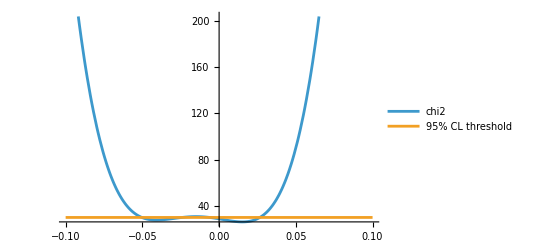

```mathematica
Plot[{LQ3chi2,min+3.841},{WC["lq3",{1,1,1,2}],-0.1,0.1},PlotLegends->{"chi2","95% CL threshold"}]
```

## C_lu

```mathematica
LUchi2binned=ChiSquareLHC["di-electron-CMS",Coefficients->{WC["lu",{1,1,1,2}]}]
```

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{1.31229×10^-7 (-220.-904.2 WC[lu,{1,1,1,2}]^2)^2,4.79709×10^-7 (-508.-1000.71 WC[lu,{1,1,1,2}]^2)^2,8.32932×10^-7 (-186.-1018.64 WC[lu,{1,1,1,2}]^2)^2,1.42801×10^-6 (-102.8-1026.57 WC[lu,{1,1,1,2}]^2)^2,2.91439×10^-6 (-95.8-1027.98 WC[lu,{1,1,1,2}]^2)^2,3.77702×10^-6 (25.4-1036.52 WC[lu,{1,1,1,2}]^2)^2,6.59321×10^-6 (-80.2-1036.38 WC[lu,{1,1,1,2}]^2)^2,0.0000119208 (10.-1004.98 WC[lu,{1,1,1,2}]^2)^2,0.0000136098 (-92.6-1018.81 WC[lu,{1,1,1,2}]^2)^2,0.000026548 (-127.2-1000.76 WC[lu,{1,1,1,2}]^2)^2,0.0000289728 (-39.8-985.534 WC[lu,{1,1,1,2}]^2)^2,0.0000610597 (15.2-972.222 WC[lu,{1,1,1,2}]^2)^2,0.0000781328 (24.-957.129 WC[lu,{1,1,1,2}]^2)^2,0.000132442 (-85.9-924.157 WC[lu,{1,1,1,2}]^2)^2,0.000175753 (-70.3-930.045 WC[lu,{1,1,1,2}]^2)^2,0.000158207 (-34.16-892.507 WC[lu,{1,1,1,2}]^2)^2,0.000303825 (-8.72-899.869 WC[lu,{1,1,1,2}]^2)^2,0.000400252 (-29.48-881.637 WC[lu,{1,1,1,2}]^2)^2,0.000474043 (9.46-838.675 WC[lu,{1,1,1,2}]^2)^2,0.000597818 (20.2-839.903 WC[lu,{1,1,1,2}]^2)^2,0.00028771 (13.24-1217.21 WC[lu,{1,1,1,2}]^2)^2,0.00067054 (9.24-1183.76 WC[lu,{1,1,1,2}]^2)^2,0.000826956 (1.31-1151.43 WC[lu,{1,1,1,2}]^2)^2,0.00103064 (20.23-1088.22 WC[lu,{1,1,1,2}]^2)^2,0.00138021 (43.85-1052.9 WC[lu,{1,1,1,2}]^2)^2,0.00172993 (44.09-1022.29 WC[lu,{1,1,1,2}]^2)^2,0.00225394 (-39.474-986.426 WC[lu,{1,1,1,2}]^2)^2,0.00205416 (20.313-943.476 WC[lu,{1,1,1,2}]^2)^2,0.00439089 (-3.942-923.967 WC[lu,{1,1,1,2}]^2)^2,0.00550609 (-10.403-874.462 WC[lu,{1,1,1,2}]^2)^2,0.00277449 (-3.095-1378.85 WC[lu,{1,1,1,2}]^2)^2,0.00447406 (19.095-1298.56 WC[lu,{1,1,1,2}]^2)^2,0.00784357 (-19.805-1249.32 WC[lu,{1,1,1,2}]^2)^2,0.00876178 (-1.795-1166.46 WC[lu,{1,1,1,2}]^2)^2,0.0101038 (13.785-1072. WC[lu,{1,1,1,2}]^2)^2,0.0159493 (-3.115-1009.45 WC[lu,{1,1,1,2}]^2)^2,0.0193558 (-0.3115-958.342 WC[lu,{1,1,1,2}]^2)^2,0.0173414 (3.643-1034.49 WC[lu,{1,1,1,2}]^2)^2,0.0257042 (1.4852-975.215 WC[lu,{1,1,1,2}]^2)^2,0.0390994 (-2.7774-903.811 WC[lu,{1,1,1,2}]^2)^2,0.0361578 (5.8864-833.052 WC[lu,{1,1,1,2}]^2)^2,0.058422 (-0.0264-766.55 WC[lu,{1,1,1,2}]^2)^2,0.0392055 (-0.3364-1482.27 WC[lu,{1,1,1,2}]^2)^2,0.0549663 (1.64935-1350.04 WC[lu,{1,1,1,2}]^2)^2,0.0603729 (6.03191-1186.97 WC[lu,{1,1,1,2}]^2)^2,0.0811921 (3.32544-1481.73 WC[lu,{1,1,1,2}]^2)^2,0.0708141 (5.30038-3957.56 WC[lu,{1,1,1,2}]^2)^2}

```mathematica
LUchi2binned // Length
```

47

```mathematica
WC/:Conjugate[WC[a___]]:=WC[a]
```

```mathematica
LUchi2=Total[LUchi2binned]
```

0.0708141 (5.30038-3957.56 WC[lu,{1,1,1,2}]^2)^2+0.0392055 (-0.3364-1482.27 WC[lu,{1,1,1,2}]^2)^2+0.0811921 (3.32544-1481.73 WC[lu,{1,1,1,2}]^2)^2+0.00277449 (-3.095-1378.85 WC[lu,{1,1,1,2}]^2)^2+0.0549663 (1.64935-1350.04 WC[lu,{1,1,1,2}]^2)^2+0.00447406 (19.095-1298.56 WC[lu,{1,1,1,2}]^2)^2+0.00784357 (-19.805-1249.32 WC[lu,{1,1,1,2}]^2)^2+0.00028771 (13.24-1217.21 WC[lu,{1,1,1,2}]^2)^2+0.0603729 (6.03191-1186.97 WC[lu,{1,1,1,2}]^2)^2+0.00067054 (9.24-1183.76 WC[lu,{1,1,1,2}]^2)^2+0.00876178 (-1.795-1166.46 WC[lu,{1,1,1,2}]^2)^2+0.000826956 (1.31-1151.43 WC[lu,{1,1,1,2}]^2)^2+0.00103064 (20.23-1088.22 WC[lu,{1,1,1,2}]^2)^2+0.0101038 (13.785-1072. WC[lu,{1,1,1,2}]^2)^2+0.00138021 (43.85-1052.9 WC[lu,{1,1,1,2}]^2)^2+3.77702×10^-6 (25.4-1036.52 WC[lu,{1,1,1,2}]^2)^2+6.59321×10^-6 (-80.2-1036.38 WC[lu,{1,1,1,2}]^2)^2+0.0173414 (3.643-1034.49 WC[lu,{1,1,1,2}]^2)^2+2.91439×10^-6 (-95.8-1027.98 WC[lu,{1,1,1,2}]^2)^2+1.42801×10^-6 (-102.8-1026.57 WC[lu,{1,1,1,2}]^2)^2+0.00172993 (44.09-1022.29 WC[lu,{1,1,1,2}]^2)^2+0.0000136098 (-92.6-1018.81 WC[lu,{1,1,1,2}]^2)^2+8.32932×10^-7 (-186.-1018.64 WC[lu,{1,1,1,2}]^2)^2+0.0159493 (-3.115-1009.45 WC[lu,{1,1,1,2}]^2)^2+0.0000119208 (10.-1004.98 WC[lu,{1,1,1,2}]^2)^2+0.000026548 (-127.2-1000.76 WC[lu,{1,1,1,2}]^2)^2+4.79709×10^-7 (-508.-1000.71 WC[lu,{1,1,1,2}]^2)^2+0.00225394 (-39.474-986.426 WC[lu,{1,1,1,2}]^2)^2+0.0000289728 (-39.8-985.534 WC[lu,{1,1,1,2}]^2)^2+0.0257042 (1.4852-975.215 WC[lu,{1,1,1,2}]^2)^2+0.0000610597 (15.2-972.222 WC[lu,{1,1,1,2}]^2)^2+0.0193558 (-0.3115-958.342 WC[lu,{1,1,1,2}]^2)^2+0.0000781328 (24.-957.129 WC[lu,{1,1,1,2}]^2)^2+0.00205416 (20.313-943.476 WC[lu,{1,1,1,2}]^2)^2+0.000175753 (-70.3-930.045 WC[lu,{1,1,1,2}]^2)^2+0.000132442 (-85.9-924.157 WC[lu,{1,1,1,2}]^2)^2+0.00439089 (-3.942-923.967 WC[lu,{1,1,1,2}]^2)^2+1.31229×10^-7 (-220.-904.2 WC[lu,{1,1,1,2}]^2)^2+0.0390994 (-2.7774-903.811 WC[lu,{1,1,1,2}]^2)^2+0.000303825 (-8.72-899.869 WC[lu,{1,1,1,2}]^2)^2+0.000158207 (-34.16-892.507 WC[lu,{1,1,1,2}]^2)^2+0.000400252 (-29.48-881.637 WC[lu,{1,1,1,2}]^2)^2+0.00550609 (-10.403-874.462 WC[lu,{1,1,1,2}]^2)^2+0.000597818 (20.2-839.903 WC[lu,{1,1,1,2}]^2)^2+0.000474043 (9.46-838.675 WC[lu,{1,1,1,2}]^2)^2+0.0361578 (5.8864-833.052 WC[lu,{1,1,1,2}]^2)^2+0.058422 (-0.0264-766.55 WC[lu,{1,1,1,2}]^2)^2

```mathematica
{min,bestfit}=NMinimize[LUchi2,{WC["lu",{1,1,1,2}]}]
```

{25.2717,{WC[lu,{1,1,1,2}]→0.0381458}}

```mathematica
Solve[LUchi2==min+3.841,WC["lu",{1,1,1,2}]]
```

{{WC[lu,{1,1,1,2}]→-0.0540114},{WC[lu,{1,1,1,2}]→0.-0.00265289 ⅈ},{WC[lu,{1,1,1,2}]→0.+0.00265289 ⅈ},{WC[lu,{1,1,1,2}]→0.0540114}}

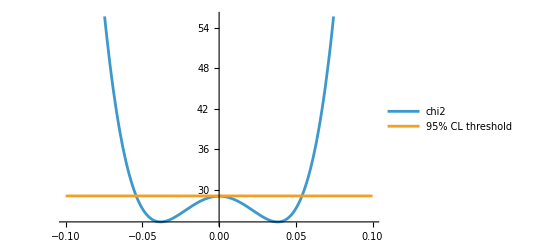

```mathematica
Plot[{LUchi2,min+3.841},{WC["lu",{1,1,1,2}],-0.1,0.1},PlotLegends->{"chi2","95% CL threshold"}]
```

## C_eq

```mathematica
EQchi2binned=ChiSquareLHC["di-electron-CMS",Coefficients->{WC["eq",{1,1,1,2}]}]
```

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{1.31229×10^-7 ((-220.+0. ⅈ)+(183.266+0. ⅈ) WC[eq,{1,1,1,2}]-1973.06 WC[eq,{1,1,1,2}]^2)^2,4.79709×10^-7 ((-508.+0. ⅈ)+(157.176+0. ⅈ) WC[eq,{1,1,1,2}]-2128.08 WC[eq,{1,1,1,2}]^2)^2,8.32932×10^-7 ((-186.+0. ⅈ)+(173.326+0. ⅈ) WC[eq,{1,1,1,2}]-2149.62 WC[eq,{1,1,1,2}]^2)^2,1.42801×10^-6 ((-102.8+0. ⅈ)+(189.229+0. ⅈ) WC[eq,{1,1,1,2}]-2197.72 WC[eq,{1,1,1,2}]^2)^2,2.91439×10^-6 ((-95.8+0. ⅈ)+(175.963+0. ⅈ) WC[eq,{1,1,1,2}]-2178.59 WC[eq,{1,1,1,2}]^2)^2,3.77702×10^-6 ((25.4+0. ⅈ)+(176.855+0. ⅈ) WC[eq,{1,1,1,2}]-2173.48 WC[eq,{1,1,1,2}]^2)^2,6.59321×10^-6 ((-80.2+0. ⅈ)+(143.83+0. ⅈ) WC[eq,{1,1,1,2}]-2154.23 WC[eq,{1,1,1,2}]^2)^2,0.0000119208 ((10.+0. ⅈ)+(147.093+0. ⅈ) WC[eq,{1,1,1,2}]-2093.89 WC[eq,{1,1,1,2}]^2)^2,0.0000136098 ((-92.6+0. ⅈ)+(127.834+0. ⅈ) WC[eq,{1,1,1,2}]-2114.65 WC[eq,{1,1,1,2}]^2)^2,0.000026548 ((-127.2+0. ⅈ)+(128.704+0. ⅈ) WC[eq,{1,1,1,2}]-2062.59 WC[eq,{1,1,1,2}]^2)^2,0.0000289728 ((-39.8+0. ⅈ)+(99.3893+0. ⅈ) WC[eq,{1,1,1,2}]-2018.67 WC[eq,{1,1,1,2}]^2)^2,0.0000610597 ((15.2+0. ⅈ)+(108.621+0. ⅈ) WC[eq,{1,1,1,2}]-1979.5 WC[eq,{1,1,1,2}]^2)^2,0.0000781328 ((24.+0. ⅈ)+(90.2391+0. ⅈ) WC[eq,{1,1,1,2}]-1959.06 WC[eq,{1,1,1,2}]^2)^2,0.000132442 ((-85.9+0. ⅈ)+(84.9624+0. ⅈ) WC[eq,{1,1,1,2}]-1911.55 WC[eq,{1,1,1,2}]^2)^2,0.000175753 ((-70.3+0. ⅈ)+(74.7179+0. ⅈ) WC[eq,{1,1,1,2}]-1872.72 WC[eq,{1,1,1,2}]^2)^2,0.000158207 ((-34.16+0. ⅈ)+(71.5862+0. ⅈ) WC[eq,{1,1,1,2}]-1810.23 WC[eq,{1,1,1,2}]^2)^2,0.000303825 ((-8.72+0. ⅈ)+(63.8005+0. ⅈ) WC[eq,{1,1,1,2}]-1785.87 WC[eq,{1,1,1,2}]^2)^2,0.000400252 ((-29.48+0. ⅈ)+(59.1301+0. ⅈ) WC[eq,{1,1,1,2}]-1767.6 WC[eq,{1,1,1,2}]^2)^2,0.000474043 ((9.46+0. ⅈ)+(61.8359+0. ⅈ) WC[eq,{1,1,1,2}]-1701.15 WC[eq,{1,1,1,2}]^2)^2,0.000597818 ((20.2+0. ⅈ)+(55.8172+0. ⅈ) WC[eq,{1,1,1,2}]-1676.85 WC[eq,{1,1,1,2}]^2)^2,0.00028771 ((13.24+0. ⅈ)+(72.4951+0. ⅈ) WC[eq,{1,1,1,2}]-2414.65 WC[eq,{1,1,1,2}]^2)^2,0.00067054 ((9.24+0. ⅈ)+(64.9168+0. ⅈ) WC[eq,{1,1,1,2}]-2346.68 WC[eq,{1,1,1,2}]^2)^2,0.000826956 ((1.31+0. ⅈ)+(61.7363+0. ⅈ) WC[eq,{1,1,1,2}]-2260.51 WC[eq,{1,1,1,2}]^2)^2,0.00103064 ((20.23+0. ⅈ)+(54.6737+0. ⅈ) WC[eq,{1,1,1,2}]-2147.36 WC[eq,{1,1,1,2}]^2)^2,0.00138021 ((43.85+0. ⅈ)+(51.5494+0. ⅈ) WC[eq,{1,1,1,2}]-2076.66 WC[eq,{1,1,1,2}]^2)^2,0.00172993 ((44.09+0. ⅈ)+(47.0274+0. ⅈ) WC[eq,{1,1,1,2}]-2001.52 WC[eq,{1,1,1,2}]^2)^2,0.00225394 ((-39.474+0. ⅈ)+(39.2074+0. ⅈ) WC[eq,{1,1,1,2}]-1936.53 WC[eq,{1,1,1,2}]^2)^2,0.00205416 ((20.313+0. ⅈ)+(33.9804+0. ⅈ) WC[eq,{1,1,1,2}]-1835.88 WC[eq,{1,1,1,2}]^2)^2,0.00439089 ((-3.942+0. ⅈ)+(38.2608+0. ⅈ) WC[eq,{1,1,1,2}]-1794.37 WC[eq,{1,1,1,2}]^2)^2,0.00550609 ((-10.403+0. ⅈ)+(33.0558+0. ⅈ) WC[eq,{1,1,1,2}]-1711.95 WC[eq,{1,1,1,2}]^2)^2,0.00277449 ((-3.095+0. ⅈ)+(48.6534+0. ⅈ) WC[eq,{1,1,1,2}]-2690.86 WC[eq,{1,1,1,2}]^2)^2,0.00447406 ((19.095+0. ⅈ)+(39.2597+0. ⅈ) WC[eq,{1,1,1,2}]-2530.92 WC[eq,{1,1,1,2}]^2)^2,0.00784357 ((-19.805+0. ⅈ)+(32.4121+0. ⅈ) WC[eq,{1,1,1,2}]-2374.04 WC[eq,{1,1,1,2}]^2)^2,0.00876178 ((-1.795+0. ⅈ)+(29.4898+0. ⅈ) WC[eq,{1,1,1,2}]-2201.41 WC[eq,{1,1,1,2}]^2)^2,0.0101038 ((13.785+0. ⅈ)+(24.3407+0. ⅈ) WC[eq,{1,1,1,2}]-2082.48 WC[eq,{1,1,1,2}]^2)^2,0.0159493 ((-3.115+0. ⅈ)+(22.2306+0. ⅈ) WC[eq,{1,1,1,2}]-1946.66 WC[eq,{1,1,1,2}]^2)^2,0.0193558 ((-0.3115+0. ⅈ)+(18.5424+0. ⅈ) WC[eq,{1,1,1,2}]-1802.37 WC[eq,{1,1,1,2}]^2)^2,0.0173414 ((3.643+0. ⅈ)+(21.1105+0. ⅈ) WC[eq,{1,1,1,2}]-1968.37 WC[eq,{1,1,1,2}]^2)^2,0.0257042 ((1.4852+0. ⅈ)+(17.7671+0. ⅈ) WC[eq,{1,1,1,2}]-1848.7 WC[eq,{1,1,1,2}]^2)^2,0.0390994 ((-2.7774+0. ⅈ)+(16.9215+0. ⅈ) WC[eq,{1,1,1,2}]-1711.91 WC[eq,{1,1,1,2}]^2)^2,0.0361578 ((5.8864+0. ⅈ)+(12.3898+0. ⅈ) WC[eq,{1,1,1,2}]-1578.09 WC[eq,{1,1,1,2}]^2)^2,0.058422 ((-0.0264+0. ⅈ)+(10.9492+0. ⅈ) WC[eq,{1,1,1,2}]-1443. WC[eq,{1,1,1,2}]^2)^2,0.0392055 ((-0.3364+0. ⅈ)+(20.5052+0. ⅈ) WC[eq,{1,1,1,2}]-2783.15 WC[eq,{1,1,1,2}]^2)^2,0.0549663 ((1.64935+0. ⅈ)+(15.6082+0. ⅈ) WC[eq,{1,1,1,2}]-2510.64 WC[eq,{1,1,1,2}]^2)^2,0.0603729 ((6.03191+0. ⅈ)+(12.2091+0. ⅈ) WC[eq,{1,1,1,2}]-2218.83 WC[eq,{1,1,1,2}]^2)^2,0.0811921 ((3.32544+0. ⅈ)+(13.2849+0. ⅈ) WC[eq,{1,1,1,2}]-2757.38 WC[eq,{1,1,1,2}]^2)^2,0.0708141 ((5.30038+0. ⅈ)+(21.584+0. ⅈ) WC[eq,{1,1,1,2}]-7179.07 WC[eq,{1,1,1,2}]^2)^2}

```mathematica
EQchi2binned // Length
```

47

```mathematica
WC/:Conjugate[WC[a___]]:=WC[a]
```

```mathematica
EQchi2=Total[EQchi2binned]
```

0.0708141 ((5.30038+0. ⅈ)+(21.584+0. ⅈ) WC[eq,{1,1,1,2}]-7179.07 WC[eq,{1,1,1,2}]^2)^2+0.0392055 ((-0.3364+0. ⅈ)+(20.5052+0. ⅈ) WC[eq,{1,1,1,2}]-2783.15 WC[eq,{1,1,1,2}]^2)^2+0.0811921 ((3.32544+0. ⅈ)+(13.2849+0. ⅈ) WC[eq,{1,1,1,2}]-2757.38 WC[eq,{1,1,1,2}]^2)^2+0.00277449 ((-3.095+0. ⅈ)+(48.6534+0. ⅈ) WC[eq,{1,1,1,2}]-2690.86 WC[eq,{1,1,1,2}]^2)^2+0.00447406 ((19.095+0. ⅈ)+(39.2597+0. ⅈ) WC[eq,{1,1,1,2}]-2530.92 WC[eq,{1,1,1,2}]^2)^2+0.0549663 ((1.64935+0. ⅈ)+(15.6082+0. ⅈ) WC[eq,{1,1,1,2}]-2510.64 WC[eq,{1,1,1,2}]^2)^2+0.00028771 ((13.24+0. ⅈ)+(72.4951+0. ⅈ) WC[eq,{1,1,1,2}]-2414.65 WC[eq,{1,1,1,2}]^2)^2+0.00784357 ((-19.805+0. ⅈ)+(32.4121+0. ⅈ) WC[eq,{1,1,1,2}]-2374.04 WC[eq,{1,1,1,2}]^2)^2+0.00067054 ((9.24+0. ⅈ)+(64.9168+0. ⅈ) WC[eq,{1,1,1,2}]-2346.68 WC[eq,{1,1,1,2}]^2)^2+0.000826956 ((1.31+0. ⅈ)+(61.7363+0. ⅈ) WC[eq,{1,1,1,2}]-2260.51 WC[eq,{1,1,1,2}]^2)^2+0.0603729 ((6.03191+0. ⅈ)+(12.2091+0. ⅈ) WC[eq,{1,1,1,2}]-2218.83 WC[eq,{1,1,1,2}]^2)^2+0.00876178 ((-1.795+0. ⅈ)+(29.4898+0. ⅈ) WC[eq,{1,1,1,2}]-2201.41 WC[eq,{1,1,1,2}]^2)^2+1.42801×10^-6 ((-102.8+0. ⅈ)+(189.229+0. ⅈ) WC[eq,{1,1,1,2}]-2197.72 WC[eq,{1,1,1,2}]^2)^2+2.91439×10^-6 ((-95.8+0. ⅈ)+(175.963+0. ⅈ) WC[eq,{1,1,1,2}]-2178.59 WC[eq,{1,1,1,2}]^2)^2+3.77702×10^-6 ((25.4+0. ⅈ)+(176.855+0. ⅈ) WC[eq,{1,1,1,2}]-2173.48 WC[eq,{1,1,1,2}]^2)^2+6.59321×10^-6 ((-80.2+0. ⅈ)+(143.83+0. ⅈ) WC[eq,{1,1,1,2}]-2154.23 WC[eq,{1,1,1,2}]^2)^2+8.32932×10^-7 ((-186.+0. ⅈ)+(173.326+0. ⅈ) WC[eq,{1,1,1,2}]-2149.62 WC[eq,{1,1,1,2}]^2)^2+0.00103064 ((20.23+0. ⅈ)+(54.6737+0. ⅈ) WC[eq,{1,1,1,2}]-2147.36 WC[eq,{1,1,1,2}]^2)^2+4.79709×10^-7 ((-508.+0. ⅈ)+(157.176+0. ⅈ) WC[eq,{1,1,1,2}]-2128.08 WC[eq,{1,1,1,2}]^2)^2+0.0000136098 ((-92.6+0. ⅈ)+(127.834+0. ⅈ) WC[eq,{1,1,1,2}]-2114.65 WC[eq,{1,1,1,2}]^2)^2+0.0000119208 ((10.+0. ⅈ)+(147.093+0. ⅈ) WC[eq,{1,1,1,2}]-2093.89 WC[eq,{1,1,1,2}]^2)^2+0.0101038 ((13.785+0. ⅈ)+(24.3407+0. ⅈ) WC[eq,{1,1,1,2}]-2082.48 WC[eq,{1,1,1,2}]^2)^2+0.00138021 ((43.85+0. ⅈ)+(51.5494+0. ⅈ) WC[eq,{1,1,1,2}]-2076.66 WC[eq,{1,1,1,2}]^2)^2+0.000026548 ((-127.2+0. ⅈ)+(128.704+0. ⅈ) WC[eq,{1,1,1,2}]-2062.59 WC[eq,{1,1,1,2}]^2)^2+0.0000289728 ((-39.8+0. ⅈ)+(99.3893+0. ⅈ) WC[eq,{1,1,1,2}]-2018.67 WC[eq,{1,1,1,2}]^2)^2+0.00172993 ((44.09+0. ⅈ)+(47.0274+0. ⅈ) WC[eq,{1,1,1,2}]-2001.52 WC[eq,{1,1,1,2}]^2)^2+0.0000610597 ((15.2+0. ⅈ)+(108.621+0. ⅈ) WC[eq,{1,1,1,2}]-1979.5 WC[eq,{1,1,1,2}]^2)^2+1.31229×10^-7 ((-220.+0. ⅈ)+(183.266+0. ⅈ) WC[eq,{1,1,1,2}]-1973.06 WC[eq,{1,1,1,2}]^2)^2+0.0173414 ((3.643+0. ⅈ)+(21.1105+0. ⅈ) WC[eq,{1,1,1,2}]-1968.37 WC[eq,{1,1,1,2}]^2)^2+0.0000781328 ((24.+0. ⅈ)+(90.2391+0. ⅈ) WC[eq,{1,1,1,2}]-1959.06 WC[eq,{1,1,1,2}]^2)^2+0.0159493 ((-3.115+0. ⅈ)+(22.2306+0. ⅈ) WC[eq,{1,1,1,2}]-1946.66 WC[eq,{1,1,1,2}]^2)^2+0.00225394 ((-39.474+0. ⅈ)+(39.2074+0. ⅈ) WC[eq,{1,1,1,2}]-1936.53 WC[eq,{1,1,1,2}]^2)^2+0.000132442 ((-85.9+0. ⅈ)+(84.9624+0. ⅈ) WC[eq,{1,1,1,2}]-1911.55 WC[eq,{1,1,1,2}]^2)^2+0.000175753 ((-70.3+0. ⅈ)+(74.7179+0. ⅈ) WC[eq,{1,1,1,2}]-1872.72 WC[eq,{1,1,1,2}]^2)^2+0.0257042 ((1.4852+0. ⅈ)+(17.7671+0. ⅈ) WC[eq,{1,1,1,2}]-1848.7 WC[eq,{1,1,1,2}]^2)^2+0.00205416 ((20.313+0. ⅈ)+(33.9804+0. ⅈ) WC[eq,{1,1,1,2}]-1835.88 WC[eq,{1,1,1,2}]^2)^2+0.000158207 ((-34.16+0. ⅈ)+(71.5862+0. ⅈ) WC[eq,{1,1,1,2}]-1810.23 WC[eq,{1,1,1,2}]^2)^2+0.0193558 ((-0.3115+0. ⅈ)+(18.5424+0. ⅈ) WC[eq,{1,1,1,2}]-1802.37 WC[eq,{1,1,1,2}]^2)^2+0.00439089 ((-3.942+0. ⅈ)+(38.2608+0. ⅈ) WC[eq,{1,1,1,2}]-1794.37 WC[eq,{1,1,1,2}]^2)^2+0.000303825 ((-8.72+0. ⅈ)+(63.8005+0. ⅈ) WC[eq,{1,1,1,2}]-1785.87 WC[eq,{1,1,1,2}]^2)^2+0.000400252 ((-29.48+0. ⅈ)+(59.1301+0. ⅈ) WC[eq,{1,1,1,2}]-1767.6 WC[eq,{1,1,1,2}]^2)^2+0.00550609 ((-10.403+0. ⅈ)+(33.0558+0. ⅈ) WC[eq,{1,1,1,2}]-1711.95 WC[eq,{1,1,1,2}]^2)^2+0.0390994 ((-2.7774+0. ⅈ)+(16.9215+0. ⅈ) WC[eq,{1,1,1,2}]-1711.91 WC[eq,{1,1,1,2}]^2)^2+0.000474043 ((9.46+0. ⅈ)+(61.8359+0. ⅈ) WC[eq,{1,1,1,2}]-1701.15 WC[eq,{1,1,1,2}]^2)^2+0.000597818 ((20.2+0. ⅈ)+(55.8172+0. ⅈ) WC[eq,{1,1,1,2}]-1676.85 WC[eq,{1,1,1,2}]^2)^2+0.0361578 ((5.8864+0. ⅈ)+(12.3898+0. ⅈ) WC[eq,{1,1,1,2}]-1578.09 WC[eq,{1,1,1,2}]^2)^2+0.058422 ((-0.0264+0. ⅈ)+(10.9492+0. ⅈ) WC[eq,{1,1,1,2}]-1443. WC[eq,{1,1,1,2}]^2)^2

```mathematica
{min,bestfit}=NMinimize[EQchi2,{WC["eq",{1,1,1,2}]}]
```

{25.149+0. ⅈ,{WC[eq,{1,1,1,2}]→0.0307595+0. ⅈ}}

```mathematica
Solve[EQchi2==min+3.841,WC["eq",{1,1,1,2}]]
```

{{WC[eq,{1,1,1,2}]→-0.0368616},{WC[eq,{1,1,1,2}]→-0.00153439},{WC[eq,{1,1,1,2}]→0.0058878},{WC[eq,{1,1,1,2}]→0.0423928}}

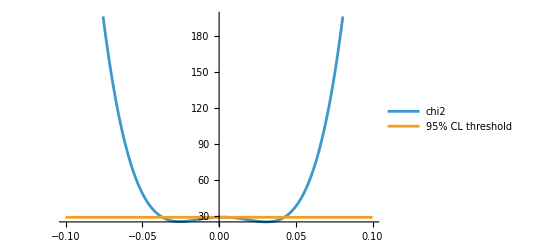

```mathematica
Plot[{EQchi2,min+3.841},{WC["eq",{1,1,1,2}],-0.1,0.1},PlotLegends->{"chi2","95% CL threshold"}]
```

## C_lequ1

```mathematica
LEQU1chi2binned=ChiSquareLHC["di-electron-CMS",Coefficients->{WC["lequ1",{1,1,2,1}]}]
```

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{1.31229×10^-7 (-220.-786.226 WC[lequ1,{1,1,2,1}]^2)^2,4.79709×10^-7 (-508.-832.035 WC[lequ1,{1,1,2,1}]^2)^2,8.32932×10^-7 (-186.-873.905 WC[lequ1,{1,1,2,1}]^2)^2,1.42801×10^-6 (-102.8-896.321 WC[lequ1,{1,1,2,1}]^2)^2,2.91439×10^-6 (-95.8-879.223 WC[lequ1,{1,1,2,1}]^2)^2,3.77702×10^-6 (25.4-860.405 WC[lequ1,{1,1,2,1}]^2)^2,6.59321×10^-6 (-80.2-889.541 WC[lequ1,{1,1,2,1}]^2)^2,0.0000119208 (10.-887.272 WC[lequ1,{1,1,2,1}]^2)^2,0.0000136098 (-92.6-881.07 WC[lequ1,{1,1,2,1}]^2)^2,0.000026548 (-127.2-869.076 WC[lequ1,{1,1,2,1}]^2)^2,0.0000289728 (-39.8-839.596 WC[lequ1,{1,1,2,1}]^2)^2,0.0000610597 (15.2-855.816 WC[lequ1,{1,1,2,1}]^2)^2,0.0000781328 (24.-826.943 WC[lequ1,{1,1,2,1}]^2)^2,0.000132442 (-85.9-830.874 WC[lequ1,{1,1,2,1}]^2)^2,0.000175753 (-70.3-788.19 WC[lequ1,{1,1,2,1}]^2)^2,0.000158207 (-34.16-775.566 WC[lequ1,{1,1,2,1}]^2)^2,0.000303825 (-8.72-767.422 WC[lequ1,{1,1,2,1}]^2)^2,0.000400252 (-29.48-755.529 WC[lequ1,{1,1,2,1}]^2)^2,0.000474043 (9.46-741.449 WC[lequ1,{1,1,2,1}]^2)^2,0.000597818 (20.2-714.453 WC[lequ1,{1,1,2,1}]^2)^2,0.00028771 (13.24-1060.66 WC[lequ1,{1,1,2,1}]^2)^2,0.00067054 (9.24-1026.79 WC[lequ1,{1,1,2,1}]^2)^2,0.000826956 (1.31-991.121 WC[lequ1,{1,1,2,1}]^2)^2,0.00103064 (20.23-957.544 WC[lequ1,{1,1,2,1}]^2)^2,0.00138021 (43.85-918.402 WC[lequ1,{1,1,2,1}]^2)^2,0.00172993 (44.09-904.846 WC[lequ1,{1,1,2,1}]^2)^2,0.00225394 (-39.474-844.172 WC[lequ1,{1,1,2,1}]^2)^2,0.00205416 (20.313-827.718 WC[lequ1,{1,1,2,1}]^2)^2,0.00439089 (-3.942-808.487 WC[lequ1,{1,1,2,1}]^2)^2,0.00550609 (-10.403-773.123 WC[lequ1,{1,1,2,1}]^2)^2,0.00277449 (-3.095-1248.68 WC[lequ1,{1,1,2,1}]^2)^2,0.00447406 (19.095-1156.25 WC[lequ1,{1,1,2,1}]^2)^2,0.00784357 (-19.805-1083.77 WC[lequ1,{1,1,2,1}]^2)^2,0.00876178 (-1.795-1005.24 WC[lequ1,{1,1,2,1}]^2)^2,0.0101038 (13.785-961.917 WC[lequ1,{1,1,2,1}]^2)^2,0.0159493 (-3.115-902.032 WC[lequ1,{1,1,2,1}]^2)^2,0.0193558 (-0.3115-817.519 WC[lequ1,{1,1,2,1}]^2)^2,0.0173414 (3.643-965.485 WC[lequ1,{1,1,2,1}]^2)^2,0.0257042 (1.4852-862.655 WC[lequ1,{1,1,2,1}]^2)^2,0.0390994 (-2.7774-802.32 WC[lequ1,{1,1,2,1}]^2)^2,0.0361578 (5.8864-746.758 WC[lequ1,{1,1,2,1}]^2)^2,0.058422 (-0.0264-691.905 WC[lequ1,{1,1,2,1}]^2)^2,0.0392055 (-0.3364-1347.11 WC[lequ1,{1,1,2,1}]^2)^2,0.0549663 (1.64935-1211.45 WC[lequ1,{1,1,2,1}]^2)^2,0.0603729 (6.03191-1081.94 WC[lequ1,{1,1,2,1}]^2)^2,0.0811921 (3.32544-1363.06 WC[lequ1,{1,1,2,1}]^2)^2,0.0708141 (5.30038-3705.2 WC[lequ1,{1,1,2,1}]^2)^2}

```mathematica
LEQU3chi2 // Length
```

47

```mathematica
WC/:Conjugate[WC[a___]]:=WC[a]
```

```mathematica
LEQU1chi2=Total[LEQU1chi2binned]
```

0.0708141 (5.30038-3705.2 WC[lequ1,{1,1,2,1}]^2)^2+0.0811921 (3.32544-1363.06 WC[lequ1,{1,1,2,1}]^2)^2+0.0392055 (-0.3364-1347.11 WC[lequ1,{1,1,2,1}]^2)^2+0.00277449 (-3.095-1248.68 WC[lequ1,{1,1,2,1}]^2)^2+0.0549663 (1.64935-1211.45 WC[lequ1,{1,1,2,1}]^2)^2+0.00447406 (19.095-1156.25 WC[lequ1,{1,1,2,1}]^2)^2+0.00784357 (-19.805-1083.77 WC[lequ1,{1,1,2,1}]^2)^2+0.0603729 (6.03191-1081.94 WC[lequ1,{1,1,2,1}]^2)^2+0.00028771 (13.24-1060.66 WC[lequ1,{1,1,2,1}]^2)^2+0.00067054 (9.24-1026.79 WC[lequ1,{1,1,2,1}]^2)^2+0.00876178 (-1.795-1005.24 WC[lequ1,{1,1,2,1}]^2)^2+0.000826956 (1.31-991.121 WC[lequ1,{1,1,2,1}]^2)^2+0.0173414 (3.643-965.485 WC[lequ1,{1,1,2,1}]^2)^2+0.0101038 (13.785-961.917 WC[lequ1,{1,1,2,1}]^2)^2+0.00103064 (20.23-957.544 WC[lequ1,{1,1,2,1}]^2)^2+0.00138021 (43.85-918.402 WC[lequ1,{1,1,2,1}]^2)^2+0.00172993 (44.09-904.846 WC[lequ1,{1,1,2,1}]^2)^2+0.0159493 (-3.115-902.032 WC[lequ1,{1,1,2,1}]^2)^2+1.42801×10^-6 (-102.8-896.321 WC[lequ1,{1,1,2,1}]^2)^2+6.59321×10^-6 (-80.2-889.541 WC[lequ1,{1,1,2,1}]^2)^2+0.0000119208 (10.-887.272 WC[lequ1,{1,1,2,1}]^2)^2+0.0000136098 (-92.6-881.07 WC[lequ1,{1,1,2,1}]^2)^2+2.91439×10^-6 (-95.8-879.223 WC[lequ1,{1,1,2,1}]^2)^2+8.32932×10^-7 (-186.-873.905 WC[lequ1,{1,1,2,1}]^2)^2+0.000026548 (-127.2-869.076 WC[lequ1,{1,1,2,1}]^2)^2+0.0257042 (1.4852-862.655 WC[lequ1,{1,1,2,1}]^2)^2+3.77702×10^-6 (25.4-860.405 WC[lequ1,{1,1,2,1}]^2)^2+0.0000610597 (15.2-855.816 WC[lequ1,{1,1,2,1}]^2)^2+0.00225394 (-39.474-844.172 WC[lequ1,{1,1,2,1}]^2)^2+0.0000289728 (-39.8-839.596 WC[lequ1,{1,1,2,1}]^2)^2+4.79709×10^-7 (-508.-832.035 WC[lequ1,{1,1,2,1}]^2)^2+0.000132442 (-85.9-830.874 WC[lequ1,{1,1,2,1}]^2)^2+0.00205416 (20.313-827.718 WC[lequ1,{1,1,2,1}]^2)^2+0.0000781328 (24.-826.943 WC[lequ1,{1,1,2,1}]^2)^2+0.0193558 (-0.3115-817.519 WC[lequ1,{1,1,2,1}]^2)^2+0.00439089 (-3.942-808.487 WC[lequ1,{1,1,2,1}]^2)^2+0.0390994 (-2.7774-802.32 WC[lequ1,{1,1,2,1}]^2)^2+0.000175753 (-70.3-788.19 WC[lequ1,{1,1,2,1}]^2)^2+1.31229×10^-7 (-220.-786.226 WC[lequ1,{1,1,2,1}]^2)^2+0.000158207 (-34.16-775.566 WC[lequ1,{1,1,2,1}]^2)^2+0.00550609 (-10.403-773.123 WC[lequ1,{1,1,2,1}]^2)^2+0.000303825 (-8.72-767.422 WC[lequ1,{1,1,2,1}]^2)^2+0.000400252 (-29.48-755.529 WC[lequ1,{1,1,2,1}]^2)^2+0.0361578 (5.8864-746.758 WC[lequ1,{1,1,2,1}]^2)^2+0.000474043 (9.46-741.449 WC[lequ1,{1,1,2,1}]^2)^2+0.000597818 (20.2-714.453 WC[lequ1,{1,1,2,1}]^2)^2+0.058422 (-0.0264-691.905 WC[lequ1,{1,1,2,1}]^2)^2

```mathematica
{min,bestfit}=NMinimize[LEQU1chi2,{WC["lequ1",{1,1,2,1}]}]
```

{25.2298,{WC[lequ1,{1,1,2,1}]→0.0397938}}

```mathematica
Solve[LEQU1chi2==min+3.841,WC["lequ1",{1,1,2,1}]]
```

{{WC[lequ1,{1,1,2,1}]→-0.0562678},{WC[lequ1,{1,1,2,1}]→-0.00101655},{WC[lequ1,{1,1,2,1}]→0.00101655},{WC[lequ1,{1,1,2,1}]→0.0562678}}

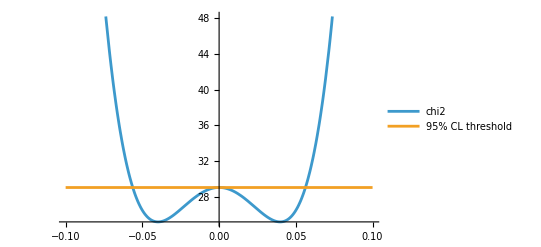

```mathematica
Plot[{LEQU1chi2,min+3.841},{WC["lequ1",{1,1,2,1}],-0.1,0.1},PlotLegends->{"chi2","95% CL threshold"}]
```

## C_lequ3

```mathematica
LEQU3chi2binned=ChiSquareLHC["di-electron-CMS",Coefficients->{WC["lequ3",{1,1,2,1}]}]
```

PROCESS | : | pp → e^-e^+
EXPERIMENT | : | CMS
ARXIV | : | [arXiv:2103.02708](https://arxiv.org/abs/2103.02708)
SOURCE | : | [hepdata: Table 3](https://doi.org/10.17182/hepdata.101186.v2/t3)
OBSERVABLE | : | m_ee
BINNING m_ee [GeV] | : | {200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,630,660,690,720,750,780,810,840,870,900,950,1000,1050,1100,1150,1200,1250,1310,1370,1430,1490,1550,1610,1680,1750,1820,1890,1970,2050,2130,2210,2290,2370,2450,2530,2610,2690,2770,2850,2930,3010,3090,3170,3250,3330,3410,3490,3570,3650,3730,3810,3890,3970,4070,4170,4270,4370,4470,4570,4670,4770,4870,4970,5070,5170,5270,5370,5470,5570,5670,5770,5870,5970,6070}
EVENTS OBSERVED | : | {51164, 36436, 26302, 19516, 14567, 11186, 8636, 6792, 5293, 4123, 3360, 2759, 2228, 1748, 1528, 1234, 1059, 864, 751, 661, 793, 639, 515, 433, 374, 311, 204, 207, 156, 124, 177, 156, 86, 78, 78, 49, 41, 43, 32, 21, 25, 15, 15, 8, 11, 6, 8, 8, 7, 3, 2, 6, 0, 1, 0, 2, 1, 0, 2, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}
LUMINOSITY [fb^-1] | : | 137
BINNING √(ŝ) [GeV] | : | {200,300,400,500,600,700,800,900,1000,1200,1400,1600,1800,2000,2250,2500,2750,3000,3500,4000,10000}
BINNING p_T [GeV] | : | {0,∞}

{1.31229×10^-7 (-220.-2903.79 WC[lequ3,{1,1,2,1}]^2)^2,4.79709×10^-7 (-508.-3120.74 WC[lequ3,{1,1,2,1}]^2)^2,8.32932×10^-7 (-186.-3198.56 WC[lequ3,{1,1,2,1}]^2)^2,1.42801×10^-6 (-102.8-3339.06 WC[lequ3,{1,1,2,1}]^2)^2,2.91439×10^-6 (-95.8-3406.02 WC[lequ3,{1,1,2,1}]^2)^2,3.77702×10^-6 (25.4-3369.26 WC[lequ3,{1,1,2,1}]^2)^2,6.59321×10^-6 (-80.2-3383.61 WC[lequ3,{1,1,2,1}]^2)^2,0.0000119208 (10.-3384.18 WC[lequ3,{1,1,2,1}]^2)^2,0.0000136098 (-92.6-3318.83 WC[lequ3,{1,1,2,1}]^2)^2,0.000026548 (-127.2-3353.09 WC[lequ3,{1,1,2,1}]^2)^2,0.0000289728 (-39.8-3409.49 WC[lequ3,{1,1,2,1}]^2)^2,0.0000610597 (15.2-3269.45 WC[lequ3,{1,1,2,1}]^2)^2,0.0000781328 (24.-3290.76 WC[lequ3,{1,1,2,1}]^2)^2,0.000132442 (-85.9-3284.31 WC[lequ3,{1,1,2,1}]^2)^2,0.000175753 (-70.3-3218.51 WC[lequ3,{1,1,2,1}]^2)^2,0.000158207 (-34.16-3200.28 WC[lequ3,{1,1,2,1}]^2)^2,0.000303825 (-8.72-3104.24 WC[lequ3,{1,1,2,1}]^2)^2,0.000400252 (-29.48-3090.32 WC[lequ3,{1,1,2,1}]^2)^2,0.000474043 (9.46-3008.8 WC[lequ3,{1,1,2,1}]^2)^2,0.000597818 (20.2-2932.68 WC[lequ3,{1,1,2,1}]^2)^2,0.00028771 (13.24-4240.14 WC[lequ3,{1,1,2,1}]^2)^2,0.00067054 (9.24-4289.92 WC[lequ3,{1,1,2,1}]^2)^2,0.000826956 (1.31-4060.01 WC[lequ3,{1,1,2,1}]^2)^2,0.00103064 (20.23-4022.66 WC[lequ3,{1,1,2,1}]^2)^2,0.00138021 (43.85-3829.91 WC[lequ3,{1,1,2,1}]^2)^2,0.00172993 (44.09-3745.63 WC[lequ3,{1,1,2,1}]^2)^2,0.00225394 (-39.474-3653.73 WC[lequ3,{1,1,2,1}]^2)^2,0.00205416 (20.313-3498.65 WC[lequ3,{1,1,2,1}]^2)^2,0.00439089 (-3.942-3393.6 WC[lequ3,{1,1,2,1}]^2)^2,0.00550609 (-10.403-3273.89 WC[lequ3,{1,1,2,1}]^2)^2,0.00277449 (-3.095-5242.7 WC[lequ3,{1,1,2,1}]^2)^2,0.00447406 (19.095-4969.34 WC[lequ3,{1,1,2,1}]^2)^2,0.00784357 (-19.805-4757.41 WC[lequ3,{1,1,2,1}]^2)^2,0.00876178 (-1.795-4325.15 WC[lequ3,{1,1,2,1}]^2)^2,0.0101038 (13.785-4136.61 WC[lequ3,{1,1,2,1}]^2)^2,0.0159493 (-3.115-3814.08 WC[lequ3,{1,1,2,1}]^2)^2,0.0193558 (-0.3115-3552.12 WC[lequ3,{1,1,2,1}]^2)^2,0.0173414 (3.643-4111.56 WC[lequ3,{1,1,2,1}]^2)^2,0.0257042 (1.4852-3833.62 WC[lequ3,{1,1,2,1}]^2)^2,0.0390994 (-2.7774-3516.23 WC[lequ3,{1,1,2,1}]^2)^2,0.0361578 (5.8864-3271.27 WC[lequ3,{1,1,2,1}]^2)^2,0.058422 (-0.0264-3014.46 WC[lequ3,{1,1,2,1}]^2)^2,0.0392055 (-0.3364-5758.66 WC[lequ3,{1,1,2,1}]^2)^2,0.0549663 (1.64935-5374.35 WC[lequ3,{1,1,2,1}]^2)^2,0.0603729 (6.03191-4698.13 WC[lequ3,{1,1,2,1}]^2)^2,0.0811921 (3.32544-5903.06 WC[lequ3,{1,1,2,1}]^2)^2,0.0708141 (5.30038-16062.2 WC[lequ3,{1,1,2,1}]^2)^2}

```mathematica
LEQU3chi2binned // Length
```

47

```mathematica
WC/:Conjugate[WC[a___]]:=WC[a]
```

```mathematica
LEQU3chi2=Total[LEQU3chi2binned]
```

0.0708141 (5.30038-16062.2 WC[lequ3,{1,1,2,1}]^2)^2+0.0811921 (3.32544-5903.06 WC[lequ3,{1,1,2,1}]^2)^2+0.0392055 (-0.3364-5758.66 WC[lequ3,{1,1,2,1}]^2)^2+0.0549663 (1.64935-5374.35 WC[lequ3,{1,1,2,1}]^2)^2+0.00277449 (-3.095-5242.7 WC[lequ3,{1,1,2,1}]^2)^2+0.00447406 (19.095-4969.34 WC[lequ3,{1,1,2,1}]^2)^2+0.00784357 (-19.805-4757.41 WC[lequ3,{1,1,2,1}]^2)^2+0.0603729 (6.03191-4698.13 WC[lequ3,{1,1,2,1}]^2)^2+0.00876178 (-1.795-4325.15 WC[lequ3,{1,1,2,1}]^2)^2+0.00067054 (9.24-4289.92 WC[lequ3,{1,1,2,1}]^2)^2+0.00028771 (13.24-4240.14 WC[lequ3,{1,1,2,1}]^2)^2+0.0101038 (13.785-4136.61 WC[lequ3,{1,1,2,1}]^2)^2+0.0173414 (3.643-4111.56 WC[lequ3,{1,1,2,1}]^2)^2+0.000826956 (1.31-4060.01 WC[lequ3,{1,1,2,1}]^2)^2+0.00103064 (20.23-4022.66 WC[lequ3,{1,1,2,1}]^2)^2+0.0257042 (1.4852-3833.62 WC[lequ3,{1,1,2,1}]^2)^2+0.00138021 (43.85-3829.91 WC[lequ3,{1,1,2,1}]^2)^2+0.0159493 (-3.115-3814.08 WC[lequ3,{1,1,2,1}]^2)^2+0.00172993 (44.09-3745.63 WC[lequ3,{1,1,2,1}]^2)^2+0.00225394 (-39.474-3653.73 WC[lequ3,{1,1,2,1}]^2)^2+0.0193558 (-0.3115-3552.12 WC[lequ3,{1,1,2,1}]^2)^2+0.0390994 (-2.7774-3516.23 WC[lequ3,{1,1,2,1}]^2)^2+0.00205416 (20.313-3498.65 WC[lequ3,{1,1,2,1}]^2)^2+0.0000289728 (-39.8-3409.49 WC[lequ3,{1,1,2,1}]^2)^2+2.91439×10^-6 (-95.8-3406.02 WC[lequ3,{1,1,2,1}]^2)^2+0.00439089 (-3.942-3393.6 WC[lequ3,{1,1,2,1}]^2)^2+0.0000119208 (10.-3384.18 WC[lequ3,{1,1,2,1}]^2)^2+6.59321×10^-6 (-80.2-3383.61 WC[lequ3,{1,1,2,1}]^2)^2+3.77702×10^-6 (25.4-3369.26 WC[lequ3,{1,1,2,1}]^2)^2+0.000026548 (-127.2-3353.09 WC[lequ3,{1,1,2,1}]^2)^2+1.42801×10^-6 (-102.8-3339.06 WC[lequ3,{1,1,2,1}]^2)^2+0.0000136098 (-92.6-3318.83 WC[lequ3,{1,1,2,1}]^2)^2+0.0000781328 (24.-3290.76 WC[lequ3,{1,1,2,1}]^2)^2+0.000132442 (-85.9-3284.31 WC[lequ3,{1,1,2,1}]^2)^2+0.00550609 (-10.403-3273.89 WC[lequ3,{1,1,2,1}]^2)^2+0.0361578 (5.8864-3271.27 WC[lequ3,{1,1,2,1}]^2)^2+0.0000610597 (15.2-3269.45 WC[lequ3,{1,1,2,1}]^2)^2+0.000175753 (-70.3-3218.51 WC[lequ3,{1,1,2,1}]^2)^2+0.000158207 (-34.16-3200.28 WC[lequ3,{1,1,2,1}]^2)^2+8.32932×10^-7 (-186.-3198.56 WC[lequ3,{1,1,2,1}]^2)^2+4.79709×10^-7 (-508.-3120.74 WC[lequ3,{1,1,2,1}]^2)^2+0.000303825 (-8.72-3104.24 WC[lequ3,{1,1,2,1}]^2)^2+0.000400252 (-29.48-3090.32 WC[lequ3,{1,1,2,1}]^2)^2+0.058422 (-0.0264-3014.46 WC[lequ3,{1,1,2,1}]^2)^2+0.000474043 (9.46-3008.8 WC[lequ3,{1,1,2,1}]^2)^2+0.000597818 (20.2-2932.68 WC[lequ3,{1,1,2,1}]^2)^2+1.31229×10^-7 (-220.-2903.79 WC[lequ3,{1,1,2,1}]^2)^2

```mathematica
{min,bestfit}=NMinimize[LEQU3chi2,{WC["lequ3",{1,1,2,1}]}]
```

{25.2417,{WC[lequ3,{1,1,2,1}]→0.0190933}}

```mathematica
Solve[LEQU3chi2==min+3.841,WC["lequ3",{1,1,2,1}]]
```

{{WC[lequ3,{1,1,2,1}]→-0.0270081},{WC[lequ3,{1,1,2,1}]→0.-0.000572466 ⅈ},{WC[lequ3,{1,1,2,1}]→0.+0.000572466 ⅈ},{WC[lequ3,{1,1,2,1}]→0.0270081}}

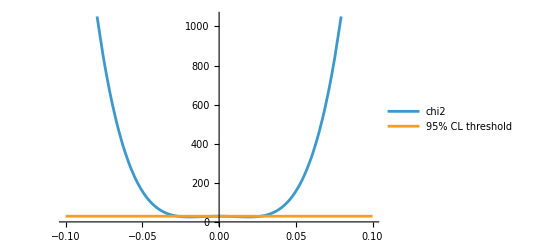

```mathematica
Plot[{LEQU3chi2,min+3.841},{WC["lequ3",{1,1,2,1}],-0.1,0.1},PlotLegends->{"chi2","95% CL threshold"}]
```